```mathematica
ClearAll["Global`*"];

shape[t0_,t1_]:=Module[{t2},{
t2=1-t0-t1;
t0*(2*t0-1),
t1*(2*t1-1),
t2*(2*t2-1),
4*t0*t1,
4*t1*t2,
4*t0*t2}];
Expand@shape[t0,t1]
Expand@shape[1-t0,1/2-t1]
Expand@shape[1-t1,1/2-(1-t0-t1)]
Expand@shape[1-(1-t0-t1),1/2-t0]

Collect[
Coefficient[Dot[{x[0],x[1],x[2],x[3],x[4],x[5]},Expand@shape[t0,t1]]+
w[0]*Dot[{x[4],x[6],x[7],x[5],x[0],x[3]},Expand@shape[1-t0,1/2-t1]]+
w[1]*Dot[{x[5],x[8],x[9],x[3],x[1],x[4]},Expand@shape[1-t1,1/2-(1-t0-t1)]]+
w[2]*Dot[{x[3],x[10],x[11],x[4],x[2],x[5]},Expand@shape[1-(1-t0-t1),1/2-t0]],Table[x[i],{i,0,11}]]
,{w[0],w[1],w[2]},FullSimplify]
```

{-t0+2 t0^2,-t1+2 t1^2,1-3 t0+2 t0^2-3 t1+4 t0 t1+2 t1^2,4 t0 t1,4 t1-4 t0 t1-4 t1^2,4 t0-4 t0^2-4 t0 t1}

{1-3 t0+2 t0^2,-t1+2 t1^2,1-3 t0+2 t0^2-3 t1+4 t0 t1+2 t1^2,2-2 t0-4 t1+4 t0 t1,-1+2 t0+4 t1-4 t0 t1-4 t1^2,-2+6 t0-4 t0^2+4 t1-4 t0 t1}

{1-3 t1+2 t1^2,1-3 t0+2 t0^2-3 t1+4 t0 t1+2 t1^2,-t0+2 t0^2,-2+4 t0+6 t1-4 t0 t1-4 t1^2,-1+4 t0-4 t0^2+2 t1-4 t0 t1,2-4 t0-2 t1+4 t0 t1}

{-t0+2 t0^2-t1+4 t0 t1+2 t1^2,-t0+2 t0^2,-t1+2 t1^2,2 t0-4 t0^2+2 t1-4 t0 t1,1-2 t0-2 t1+4 t0 t1,2 t0+2 t1-4 t0 t1-4 t1^2}

{t0 (-1+2 t0)-(-1+2 t1) (-1+2 t0+2 t1) w[0],t1 (-1+2 t1)-(-1+2 t0) (-1+2 t0+2 t1) w[1],(-1+t0+t1) (-1+2 t0+2 t1)+(-1+2 t0) (-1+2 t1) w[2],4 t0 t1-2 (-1+t0) (-1+2 t0+2 t1) w[0]-2 (-1+t1) (-1+2 t0+2 t1) w[1]+(t0+t1) (-1+2 t0+2 t1) w[2],-4 t1 (-1+t0+t1)+(-1+t0) (-1+2 t0) w[0]+2 (-1+2 t0) (-1+t1) w[1]-2 (-1+2 t0) (t0+t1) w[2],-4 t0 (-1+t0+t1)+2 (-1+t0) (-1+2 t1) w[0]+(-1+t1) (-1+2 t1) w[1]-2 (t0+t1) (-1+2 t1) w[2],t1 (-1+2 t1) w[0],(-1+t0+t1) (-1+2 t0+2 t1) w[0],(-1+t0+t1) (-1+2 t0+2 t1) w[1],t0 (-1+2 t0) w[1],t0 (-1+2 t0) w[2],t1 (-1+2 t1) w[2]}

```mathematica
Collect[
FullSimplify[Column@Collect[
Coefficient[Dot[{x[0],x[1],x[2],x[3],x[4],x[5]},Expand@shape[t0,t1]]+
w[0]*Dot[{x[4],x[6],x[7],x[5],x[0],x[3]},Expand@shape[1-t0,1/2-t1]]+
w[1]*Dot[{x[5],x[8],x[9],x[3],x[1],x[4]},Expand@shape[1-t1,1/2-(1-t0-t1)]]+
w[2]*Dot[{x[3],x[10],x[11],x[4],x[2],x[5]},Expand@shape[1-(1-t0-t1),1/2-t0]],Table[x[i],{i,0,11}]]
,{w[0],w[1],w[2]},FullSimplify]/.{(-1+t0+t1)->t2,(-1+2 t0+2 t1)->(-t2+t0+t1)}
]/.{(-1+t0+t1)->t2,(-1+2 t0+2 t1)->(-t2+t0+t1)}
,{t0,t1,t2},Simplify]
```

t0 (-1+2 t0)-(-1+2 t1) (t0+t1-t2) w[0]
t1 (-1+2 t1)-(-1+2 t0) (t0+t1-t2) w[1]
(t0+t1-t2) t2+(-1+2 t0) (-1+2 t1) w[2]
4 t0 t1-2 (-1+t0) (t0+t1-t2) w[0]-2 (-1+t1) (t0+t1-t2) w[1]+(t0+t1) (t0+t1-t2) w[2]
-4 t1 t2+(-1+t0) (-1+2 t0) w[0]+2 (-1+2 t0) (-1+t1) w[1]-2 (-1+2 t0) (t0+t1) w[2]
-4 t0 t2+2 (-1+t0) (-1+2 t1) w[0]+(-1+t1) (-1+2 t1) w[1]-2 (t0+t1) (-1+2 t1) w[2]
t1 (-1+2 t1) w[0]
(t0+t1-t2) t2 w[0]
(t0+t1-t2) t2 w[1]
t0 (-1+2 t0) w[1]
t0 (-1+2 t0) w[2]
t1 (-1+2 t1) w[2]

## 6 点の補間

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
```

```mathematica
interpQuad[points6_,t0_,t1_]:=Module[{t2},
t2=1-t0-t1;
Return[
Dot[
{t0*(2*t0-1),
t1*(2*t1-1),
t2*(2*t2-1),
4*t0*t1,
4*t1*t2,
4*t0*t2},
points6
]
];
]
interpQuadRangeChanged[points6_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN)/2;
t0=t0IN/2;
t2=1-t0-t1;
Return[
Dot[
{t0*(2*t0-1),
t1*(2*t1-1),
t2*(2*t2-1),
4*t0*t1,
4*t1*t2,
4*t0*t2},
points6
]
];
]
interpQuadRangeChanged0to1[points6_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t1=(1-t0IN+t0IN*t1IN)/2;
t0=t0IN/2;
t2=1-t0-t1;
Return[
Dot[
{t0*(2*t0-1),
t1*(2*t1-1),
t2*(2*t2-1),
4*t0*t1,
4*t1*t2,
4*t0*t2},
points6
]
];
]
Show[
ParametricPlot3D[interpQuad[ps[[1;;6]],t0,t1],{t0,0,1},{t1,0,1},PlotStyle->{Opacity[0.5]}],
ParametricPlot3D[interpQuadRangeChanged[ps[[1;;6]],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Red,Opacity[0.5]}],
ParametricPlot3D[interpQuadRangeChanged0to1[ps[[1;;6]],t0,t1],{t0,0,1},{t1,0,1},PlotStyle->{blue,Opacity[0.5]}]
]
```

-Graphics3D-

```mathematica
Ps=Table[P[i],{i,0,5}];
tmp=Simplify@Coefficient[interpQuadRangeChanged0to1[Ps,t0,t1],Ps]
Map[CForm,Simplify@tmp]/.Power->pow
```

{1/2 (-1+t0) t0,1/2 t0 (1+t0 (-1+t1)) (-1+t1),1/2 t0 t1 (-1+t0 t1),t0 (1+t0 (-1+t1)),-(1+t0 (-1+t1)) (-1+t0 t1),t0-t0^2 t1}

{((-1 + t0)*t0)/2.,(t0*(1 + t0*(-1 + t1))*(-1 + t1))/2.,(t0*t1*(-1 + t0*t1))/2.,t0*(1 + t0*(-1 + t1)),-((1 + t0*(-1 + t1))*(-1 + t0*t1)),t0 - t1*pow(t0,2)}

```mathematica
tmp=Simplify@Coefficient[D[interpQuadRangeChanged0to1[Ps,a,b],a]/.{a->t0,b->t1},Ps]
Map[CForm,Simplify@tmp]/.Power->pow
```

{-1/2+t0,1/2 (1+2 t0 (-1+t1)) (-1+t1),1/2 t1 (-1+2 t0 t1),1+2 t0 (-1+t1),-1-2 t0 (-1+t1) t1,1-2 t0 t1}

{-0.5 + t0,((1 + 2*t0*(-1 + t1))*(-1 + t1))/2.,(t1*(-1 + 2*t0*t1))/2.,1 + 2*t0*(-1 + t1),-1 - 2*t0*(-1 + t1)*t1,1 - 2*t0*t1}

```mathematica
tmp=Simplify@Coefficient[D[interpQuadRangeChanged0to1[Ps,a,b],b]/.{a->t0,b->t1},Ps]
Map[CForm,Simplify@tmp]/.Power->pow
```

{0,1/2 t0 (1+2 t0 (-1+t1)),1/2 t0 (-1+2 t0 t1),t0^2,t0^2 (1-2 t1),-t0^2}

{0,(t0*(1 + 2*t0*(-1 + t1)))/2.,(t0*(-1 + 2*t0*t1))/2.,pow(t0,2),(1 - 2*t1)*pow(t0,2),-pow(t0,2)}

## 6 x4の補間

```mathematica
ClearAll["Global`*"];

Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};

{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};

(*shapeLagQuad[t0_,t1_]:=Module[{},Return[{t0*(2*t0-1),t1*(2*t1-1),t2*(2*t2-1),4*t0*t1,4*t1*t2,4*t0*t2}];];*)
interpQuad[points6_,t0_,t1_]:=Module[{(*t2*)},
t2=1-t0-t1;
Return[
Dot[
{t0*(2*t0-1),
t1*(2*t1-1),
t2*(2*t2-1),
4*t0*t1,
4*t1*t2,
4*t0*t2},
points6
]
];
]
(*6x4の点として与えられた場合*)
interpQuadIDW64[psCenter_,ps0_,ps1_,ps2_,t0_,t1_]:=Module[{W,w,t,s,t2,sc,w0,w1,w2},
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Sum[1/(1/2-t[j]),{j,{0,1,2}}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];
Return[Dot[Table[1/(1/2-t[k]),{k,{0,1,2}}]/W,{s[0]+sc,s[1]+sc,s[2]+sc}]/2];
];
(*12点として与えられた場合*)
interpQuadIDW12[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
(*t2=1-t0-t1;
{w[0],w[1],w[2]}={1/(1/2-t0),1/(1/2-t1),1/(1/2-t2)}/(1/(1/2-t0)+1/(1/2-t1)+1/(1/2-t2));
Dot[{t0 (-1+2 t0)-(-1+2 t1) (-1+2 t0+2 t1) w[0],t1 (-1+2 t1)-(-1+2 t0) (-1+2 t0+2 t1) w[1],(-1+t0+t1) (-1+2 t0+2 t1)+(-1+2 t0) (-1+2 t1) w[2],4 t0 t1-2 (-1+t0) (-1+2 t0+2 t1) w[0]-2 (-1+t1) (-1+2 t0+2 t1) w[1]+(t0+t1) (-1+2 t0+2 t1) w[2],-4 t1 (-1+t0+t1)+(-1+t0) (-1+2 t0) w[0]+2 (-1+2 t0) (-1+t1) w[1]-2 (-1+2 t0) (t0+t1) w[2],-4 t0 (-1+t0+t1)+2 (-1+t0) (-1+2 t1) w[0]+(-1+t1) (-1+2 t1) w[1]-2 (t0+t1) (-1+2 t1) w[2],t1 (-1+2 t1) w[0],(-1+t0+t1) (-1+2 t0+2 t1) w[0],(-1+t0+t1) (-1+2 t0+2 t1) w[1],t0 (-1+2 t0) w[1],t0 (-1+2 t0) w[2],t1 (-1+2 t1) w[2]},ps]*)
Return[interpQuadIDW64[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1]];
];
(*12点として与えられた場合を形状関数との積としてプログラム*)
interpQuadIDW12Simplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=2-8 t1+8 (t0^2+t0 (-1+t1)+t1^2);
Return[1/common*Dot[
{(4 t0^2-(1-2 t1)^2-4 t0 t1) (2 t0^2+(1-2 t1)^2+t0 (-3+4 t1)),-((1-2 t0)^2+4 t0 t1-4 t1^2) ((1-2 t0)^2+(-3+4 t0) t1+2 t1^2),(t0 (-1+2 t0)+t1 (-1+2 t1)) (3-8 t1+4 ((-2+t0) t0+3 t0 t1+t1^2)),4 t0^3 (7-6 t1)+(1-2 t1)^2 (-4+7 t1)-4 t0^2 (11+2 t1 (-13+8 t1))+t0 (23-4 t1 (23-26 t1+6 t1^2)),3-8 t1+4 t0^3 (-7+6 t1)-8 t1^2 (1+2 (-2+t1) t1)+t0^2 (40-52 t1+8 t1^2)+t0 (-19+4 t1 (9+t1-8 t1^2)),3-19 t1+4 (-2 t0 (1+t0+2 (-2+t0) t0^2)+t0 (9+t0-8 t0^2) t1+(10+t0 (-13+2 t0)) t1^2+(-7+6 t0) t1^3),(1-2 t1)^2 t1 (-1+2 t0+2 t1),(-1+t0+t1) (-1+2 t1) (-1+2 t0+2 t1)^2,(-1+2 t0) (-1+t0+t1) (-1+2 t0+2 t1)^2,(1-2 t0)^2 t0 (-1+2 t0+2 t1),-(1-2 t0)^2 t0 (-1+2 t1),-(-1+2 t0) (1-2 t1)^2 t1},
ps]];
];
(*中央の三角形がt0=[0,1],t1=[0,1-t0]となる様に変換*)
interpQuadIDW12RangeChanged[ps_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN)/2;
t0=t0IN/2;
common=2-8 t1+8 (t0^2+t0 (-1+t1)+t1^2);
Return[1/common*Dot[
{(4 t0^2-(1-2 t1)^2-4 t0 t1) (2 t0^2+(1-2 t1)^2+t0 (-3+4 t1)),-((1-2 t0)^2+4 t0 t1-4 t1^2) ((1-2 t0)^2+(-3+4 t0) t1+2 t1^2),(t0 (-1+2 t0)+t1 (-1+2 t1)) (3-8 t1+4 ((-2+t0) t0+3 t0 t1+t1^2)),4 t0^3 (7-6 t1)+(1-2 t1)^2 (-4+7 t1)-4 t0^2 (11+2 t1 (-13+8 t1))+t0 (23-4 t1 (23-26 t1+6 t1^2)),3-8 t1+4 t0^3 (-7+6 t1)-8 t1^2 (1+2 (-2+t1) t1)+t0^2 (40-52 t1+8 t1^2)+t0 (-19+4 t1 (9+t1-8 t1^2)),3-19 t1+4 (-2 t0 (1+t0+2 (-2+t0) t0^2)+t0 (9+t0-8 t0^2) t1+(10+t0 (-13+2 t0)) t1^2+(-7+6 t0) t1^3),(1-2 t1)^2 t1 (-1+2 t0+2 t1),(-1+t0+t1) (-1+2 t1) (-1+2 t0+2 t1)^2,(-1+2 t0) (-1+t0+t1) (-1+2 t0+2 t1)^2,(1-2 t0)^2 t0 (-1+2 t0+2 t1),-(1-2 t0)^2 t0 (-1+2 t1),-(-1+2 t0) (1-2 t1)^2 t1},
ps]];
];
interpQuadIDW12RangeChangedSimplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0)^2 ((-1+t0)^3+(-1+t0) t0 t1+t0 t1^2);
Return[1/common*Dot[
{t0 ((-1+t0)^3-(-1+t0) t0 t1-t0 t1^2) ((-1+t0)^3+2 (-1+t0) t0 t1+2 t0 t1^2),t0 ((-1+t0)^3+(-1+t0) t1+t0 t1^2) ((-1+t0)^3+(-1+t0) (-2+3 t0) t1+t0 t1^2),-t0 ((-1+t0)^3+(-2+t0) (-1+t0) t1-t0 t1^2) (2 (-1+t0)^3+(-1+t0) (-1+2 t0) t1+t0 t1^2),(-1+t0) t0 (-2 (-1+t0)^5-(-1+t0)^3 (1+4 t0) t1+(-1+t0) (-1+(-4+t0) t0) t1^2+t0 (-7+3 t0) t1^3),-4 (-1+t0)^6+(-1+t0)^4 t0 (-8+3 t0) t1+(-1+t0)^2 t0 (8+(-11+t0) t0) t1^2-4 (-1+t0) t0^3 t1^3-2 t0^3 t1^4,(-1+t0) t0 (4 (-1+t0)^4-(-3+t0) (-1+t0)^2 (-1+3 t0) t1-(-1+t0) (1+t0 (-17+8 t0)) t1^2+(7-3 t0) t0 t1^3),t0^2 t1 (-1+t0+t1)^2 (1+t0 (-2+t0+t1)),t0^2 t1^2 (-1+t0+t1) (-1+t0+t0 t1),-(-1+t0)^2 t0 t1^2 (-1+t0+t0 t1),-(-1+t0)^5 t0 t1,(-1+t0)^5 t0 (-1+t0+t1),(-1+t0)^2 t0 (-1+t0+t1)^2 (1+t0 (-2+t0+t1))},
ps]];
];
(*中央の三角形がt0=[0,1],t1=(1-t0)*t1old=[0,1]として，両方のパラメタの範囲が[0,1]で中央三角形が得られる様に変更*)
interpQuadIDW12RangeChangedSimplifidChangeRange[ps_,t0_,t1IN_]:=Module[{t1,ps0,ps1,ps2,w,t2,common},
t1=(1-t0)t1IN;
common=4 (-1+t0)^2 ((-1+t0)^3+(-1+t0) t0 t1+t0 t1^2);
Return[1/common*Dot[
{t0 ((-1+t0)^3-(-1+t0) t0 t1-t0 t1^2) ((-1+t0)^3+2 (-1+t0) t0 t1+2 t0 t1^2),t0 ((-1+t0)^3+(-1+t0) t1+t0 t1^2) ((-1+t0)^3+(-1+t0) (-2+3 t0) t1+t0 t1^2),-t0 ((-1+t0)^3+(-2+t0) (-1+t0) t1-t0 t1^2) (2 (-1+t0)^3+(-1+t0) (-1+2 t0) t1+t0 t1^2),(-1+t0) t0 (-2 (-1+t0)^5-(-1+t0)^3 (1+4 t0) t1+(-1+t0) (-1+(-4+t0) t0) t1^2+t0 (-7+3 t0) t1^3),-4 (-1+t0)^6+(-1+t0)^4 t0 (-8+3 t0) t1+(-1+t0)^2 t0 (8+(-11+t0) t0) t1^2-4 (-1+t0) t0^3 t1^3-2 t0^3 t1^4,(-1+t0) t0 (4 (-1+t0)^4-(-3+t0) (-1+t0)^2 (-1+3 t0) t1-(-1+t0) (1+t0 (-17+8 t0)) t1^2+(7-3 t0) t0 t1^3),t0^2 t1 (-1+t0+t1)^2 (1+t0 (-2+t0+t1)),t0^2 t1^2 (-1+t0+t1) (-1+t0+t0 t1),-(-1+t0)^2 t0 t1^2 (-1+t0+t0 t1),-(-1+t0)^5 t0 t1,(-1+t0)^5 t0 (-1+t0+t1),(-1+t0)^2 t0 (-1+t0+t1)^2 (1+t0 (-2+t0+t1))},
ps]];
];
(*上を簡単化*)
interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0+t0 (-1+t1) t1);
Return[1/common*Dot[
{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2},
ps]];
];
```

## 簡単化して新たな補間関数作成の準備

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=2-8 t1+8 (t0^2+t0 (-1+t1)+t1^2);
FullSimplify[Coefficient[interpQuadIDW12[ps,t0,t1],ps]*common]
```

{(4 t0^2-(1-2 t1)^2-4 t0 t1) (2 t0^2+(1-2 t1)^2+t0 (-3+4 t1)),-((1-2 t0)^2+4 t0 t1-4 t1^2) ((1-2 t0)^2+(-3+4 t0) t1+2 t1^2),(t0 (-1+2 t0)+t1 (-1+2 t1)) (3-8 t1+4 ((-2+t0) t0+3 t0 t1+t1^2)),4 t0^3 (7-6 t1)+(1-2 t1)^2 (-4+7 t1)-4 t0^2 (11+2 t1 (-13+8 t1))+t0 (23-4 t1 (23-26 t1+6 t1^2)),3-8 t1+4 t0^3 (-7+6 t1)-8 t1^2 (1+2 (-2+t1) t1)+t0^2 (40-52 t1+8 t1^2)+t0 (-19+4 t1 (9+t1-8 t1^2)),3-19 t1+4 (-2 t0 (1+t0+2 (-2+t0) t0^2)+t0 (9+t0-8 t0^2) t1+(10+t0 (-13+2 t0)) t1^2+(-7+6 t0) t1^3),(1-2 t1)^2 t1 (-1+2 t0+2 t1),(-1+t0+t1) (-1+2 t1) (-1+2 t0+2 t1)^2,(-1+2 t0) (-1+t0+t1) (-1+2 t0+2 t1)^2,(1-2 t0)^2 t0 (-1+2 t0+2 t1),-(1-2 t0)^2 t0 (-1+2 t1),-(-1+2 t0) (1-2 t1)^2 t1}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0)^2 ((-1+t0)^3+(-1+t0) t0 t1+t0 t1^2);
FullSimplify[Coefficient[interpQuadIDW12RangeChanged[ps,t0,t1],ps]*common]
```

{t0 ((-1+t0)^3-(-1+t0) t0 t1-t0 t1^2) ((-1+t0)^3+2 (-1+t0) t0 t1+2 t0 t1^2),t0 ((-1+t0)^3+(-1+t0) t1+t0 t1^2) ((-1+t0)^3+(-1+t0) (-2+3 t0) t1+t0 t1^2),-t0 ((-1+t0)^3+(-2+t0) (-1+t0) t1-t0 t1^2) (2 (-1+t0)^3+(-1+t0) (-1+2 t0) t1+t0 t1^2),(-1+t0) t0 (-2 (-1+t0)^5-(-1+t0)^3 (1+4 t0) t1+(-1+t0) (-1+(-4+t0) t0) t1^2+t0 (-7+3 t0) t1^3),-4 (-1+t0)^6+(-1+t0)^4 t0 (-8+3 t0) t1+(-1+t0)^2 t0 (8+(-11+t0) t0) t1^2-4 (-1+t0) t0^3 t1^3-2 t0^3 t1^4,(-1+t0) t0 (4 (-1+t0)^4-(-3+t0) (-1+t0)^2 (-1+3 t0) t1-(-1+t0) (1+t0 (-17+8 t0)) t1^2+(7-3 t0) t0 t1^3),t0^2 t1 (-1+t0+t1)^2 (1+t0 (-2+t0+t1)),t0^2 t1^2 (-1+t0+t1) (-1+t0+t0 t1),-(-1+t0)^2 t0 t1^2 (-1+t0+t0 t1),-(-1+t0)^5 t0 t1,(-1+t0)^5 t0 (-1+t0+t1),(-1+t0)^2 t0 (-1+t0+t1)^2 (1+t0 (-2+t0+t1))}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0+t0 (-1+t1) t1);
FullSimplify[Coefficient[interpQuadIDW12RangeChangedSimplifidChangeRange[ps,t0,t1],ps]*common]
```

{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0 (1-t1+t1^2))^2;
Simplify[
Coefficient[
D[interpQuadIDW12RangeChangedSimplifidChangeRange[ps,a,b],a]/.{a->t0,b->t1},
ps]*common]
```

{-1+2 t0 (2-t1+t1^2)+t0^2 (-5+6 t1-t1^2-10 t1^3+5 t1^4)+2 t0^3 (1-2 t1+t1^2+4 t1^3-7 t1^4+6 t1^5-2 t1^6),-1+t1+2 t1^2-2 t0 (-2+4 t1+t1^2+t1^3)+t0^2 (-5+15 t1-11 t1^2+13 t1^3-3 t1^4+t1^5)+2 t0^3 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-5 t1+2 t1^2+2 t0 (-4+9 t1-4 t1^2+t1^3)-t0^2 (-10+25 t1-20 t1^2+11 t1^3-2 t1^4+t1^5)+2 t0^3 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),2+t1+t1^2+t0 (-8+6 t1+8 t1^2-14 t1^3)-2 t0^3 (2-6 t1+5 t1^2-4 t1^4+3 t1^5)+t0^2 (10-19 t1+17 t1^3-11 t1^4+7 t1^5),-4 (1-t1+t1^2)+t0 (8-22 t1+22 t1^2)+t0^2 (-4+24 t1-29 t1^2+10 t1^3-5 t1^4)-2 t0^3 t1 (3-4 t1+5 t1^3-6 t1^4+2 t1^5),4-3 t1+t1^2+2 t0 (-4+10 t1-17 t1^2+7 t1^3)+2 t0^3 t1 (3-11 t1+14 t1^2-11 t1^3+3 t1^4)+t0^2 (4-23 t1+55 t1^2-43 t1^3+24 t1^4-7 t1^5),t0 (-1+t1)^2 t1 (-2+t0 (-2+t1)^2+2 t0^2 (-1+2 t1-2 t1^2+t1^3)),t0 (-1+t1) t1^2 (2-t0 (1+t1)^2+2 t0^2 t1 (1-t1+t1^2)),t1^2 (-1+2 t0 (1+t1)+2 t0^3 t1 (1-t1+t1^2)-t0^2 (1+3 t1+t1^3)),(-1+t0) t1 (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t0) (-1+t1) (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t1)^2 (1+2 t0 (-2+t1)-t0^2 (-5+6 t1-3 t1^2+t1^3)+2 t0^3 (-1+2 t1-2 t1^2+t1^3))}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0 (1-t1+t1^2))^2;
Simplify[
Coefficient[
D[interpQuadIDW12RangeChangedSimplifidChangeRange[ps,a,b],b]/.{a->t0,b->t1},
ps]*common]
```

{-2 t0^3 t1 (1-3 t1+2 t1^2) (-2+t0 (2-t1+t1^2)),t0 (1+4 t1-4 t0 (1+2 t1)+t0^2 (5+2 t1+7 t1^2-6 t1^3+t1^4)+2 t0^3 (-1+t1-4 t1^2+5 t1^3-3 t1^4+t1^5)),t0 (-5+t0 (12-8 t1)+4 t1-t0^2 (9-2 t1-5 t1^2+2 t1^3+t1^4)+2 t0^3 (1+t1-3 t1^2+3 t1^3-2 t1^4+t1^5)),t0 (1+2 t1+t0 (10-19 t1) t1+t0^3 (2+6 t1-14 t1^2+6 t1^3-3 t1^4)+t0^2 (-3-18 t1+37 t1^2-14 t1^3+7 t1^4)),-t0 (-1+2 t1) (4-11 t0+t0^2 (10+4 t1-4 t1^2)+t0^3 (-3-4 t1+6 t1^2-4 t1^3+2 t1^4)),t0 (-3+2 t1+t0 (9-28 t1+19 t1^2)+t0^2 (-9+42 t1-37 t1^2+14 t1^3-7 t1^4)+t0^3 (3-16 t1+14 t1^2-6 t1^3+3 t1^4)),t0^2 (-1+t1) (1-3 t1+t0 (-2+8 t1-5 t1^2+t1^3)+t0^2 (1-5 t1+6 t1^2-4 t1^3+2 t1^4)),t0^2 t1 (-2+3 t1-t0 (-2+t1+2 t1^2+t1^3)+t0^2 t1 (-3+6 t1-4 t1^2+2 t1^3)),(-1+t0) t0 t1 (2-2 t0 (1+t1)+t0^2 t1 (3-2 t1+t1^2)),-(-1+t0)^2 t0 (1+t0 (-1+t1^2)),(-1+t0)^2 t0 (1+t0 (-2+t1) t1),-t0 (-1+t1) (2+2 t0 (-3+t1)+t0^2 (6-4 t1+t1^2-t1^3)+t0^3 (-2+2 t1-t1^2+t1^3))}

## 新たに定義し直した補間関数

```mathematica
MyinterpQuadIDW12[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0+t0 (-1+t1) t1);
Return[1/common*Dot[
{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2},
ps]];
];
MyinterpQuadIDW12Dt0[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0 (1-t1+t1^2))^2;
Return[1/common*Dot[
{-1+2 t0 (2-t1+t1^2)+t0^2 (-5+6 t1-t1^2-10 t1^3+5 t1^4)+2 t0^3 (1-2 t1+t1^2+4 t1^3-7 t1^4+6 t1^5-2 t1^6),-1+t1+2 t1^2-2 t0 (-2+4 t1+t1^2+t1^3)+t0^2 (-5+15 t1-11 t1^2+13 t1^3-3 t1^4+t1^5)+2 t0^3 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-5 t1+2 t1^2+2 t0 (-4+9 t1-4 t1^2+t1^3)-t0^2 (-10+25 t1-20 t1^2+11 t1^3-2 t1^4+t1^5)+2 t0^3 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),2+t1+t1^2+t0 (-8+6 t1+8 t1^2-14 t1^3)-2 t0^3 (2-6 t1+5 t1^2-4 t1^4+3 t1^5)+t0^2 (10-19 t1+17 t1^3-11 t1^4+7 t1^5),-4 (1-t1+t1^2)+t0 (8-22 t1+22 t1^2)+t0^2 (-4+24 t1-29 t1^2+10 t1^3-5 t1^4)-2 t0^3 t1 (3-4 t1+5 t1^3-6 t1^4+2 t1^5),4-3 t1+t1^2+2 t0 (-4+10 t1-17 t1^2+7 t1^3)+2 t0^3 t1 (3-11 t1+14 t1^2-11 t1^3+3 t1^4)+t0^2 (4-23 t1+55 t1^2-43 t1^3+24 t1^4-7 t1^5),t0 (-1+t1)^2 t1 (-2+t0 (-2+t1)^2+2 t0^2 (-1+2 t1-2 t1^2+t1^3)),t0 (-1+t1) t1^2 (2-t0 (1+t1)^2+2 t0^2 t1 (1-t1+t1^2)),t1^2 (-1+2 t0 (1+t1)+2 t0^3 t1 (1-t1+t1^2)-t0^2 (1+3 t1+t1^3)),(-1+t0) t1 (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t0) (-1+t1) (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t1)^2 (1+2 t0 (-2+t1)-t0^2 (-5+6 t1-3 t1^2+t1^3)+2 t0^3 (-1+2 t1-2 t1^2+t1^3))},
ps]];
];
MyinterpQuadIDW12Dt1[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0 (1-t1+t1^2))^2;
Return[1/common*Dot[
{-2 t0^3 t1 (1-3 t1+2 t1^2) (-2+t0 (2-t1+t1^2)),t0 (1+4 t1-4 t0 (1+2 t1)+t0^2 (5+2 t1+7 t1^2-6 t1^3+t1^4)+2 t0^3 (-1+t1-4 t1^2+5 t1^3-3 t1^4+t1^5)),t0 (-5+t0 (12-8 t1)+4 t1-t0^2 (9-2 t1-5 t1^2+2 t1^3+t1^4)+2 t0^3 (1+t1-3 t1^2+3 t1^3-2 t1^4+t1^5)),t0 (1+2 t1+t0 (10-19 t1) t1+t0^3 (2+6 t1-14 t1^2+6 t1^3-3 t1^4)+t0^2 (-3-18 t1+37 t1^2-14 t1^3+7 t1^4)),-t0 (-1+2 t1) (4-11 t0+t0^2 (10+4 t1-4 t1^2)+t0^3 (-3-4 t1+6 t1^2-4 t1^3+2 t1^4)),t0 (-3+2 t1+t0 (9-28 t1+19 t1^2)+t0^2 (-9+42 t1-37 t1^2+14 t1^3-7 t1^4)+t0^3 (3-16 t1+14 t1^2-6 t1^3+3 t1^4)),t0^2 (-1+t1) (1-3 t1+t0 (-2+8 t1-5 t1^2+t1^3)+t0^2 (1-5 t1+6 t1^2-4 t1^3+2 t1^4)),t0^2 t1 (-2+3 t1-t0 (-2+t1+2 t1^2+t1^3)+t0^2 t1 (-3+6 t1-4 t1^2+2 t1^3)),(-1+t0) t0 t1 (2-2 t0 (1+t1)+t0^2 t1 (3-2 t1+t1^2)),-(-1+t0)^2 t0 (1+t0 (-1+t1^2)),(-1+t0)^2 t0 (1+t0 (-2+t1) t1),-t0 (-1+t1) (2+2 t0 (-3+t1)+t0^2 (6-4 t1+t1^2-t1^3)+t0^3 (-2+2 t1-t1^2+t1^3))},
ps]];
];
```

## c++ へ移植

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0+t0 (-1+t1) t1);
CForm[common]
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12[ps,t0,t1],ps]*common]/.Power->pow]
```

{-(t0*(-1 + t0 + 2*t0*(-1 + t1)*t1)*(1 + t0*(-1 + (-1 + t1)*t1))),t0*(-1 + t0 + 2*t1 + t0*(-3 + t1)*t1)*(-1 + t0 - t1 + t0*pow(t1,2)),t0*(-2 + t1 + t0*(2 + (-2 + t1)*t1))*(1 - 2*t1 + t0*(-1 + t1 + pow(t1,2))),-(t0*(2 + t1 + t0*(-4 + t1*(3 + (4 - 7*t1)*t1)) + (-1 + t1)*(-2 + t1*(2 + 3*t1))*pow(t0,2) + pow(t1,2))),-4 + t0*(8 + 8*(-1 + t1)*t1 + t0*(-4 - 11*(-1 + t1)*t1) + t1*pow(t0,2)*(-3 + t1 + 4*pow(t1,2) - 2*pow(t1,3))),t0*(-4 - (-3 + t1)*t1 + t0*(4 - (-1 + t1)*t1*(-10 + 7*t1)) + t1*(3 + t1*(-8 + 3*t1))*pow(t0,2)),(1 + t0*(-1 + t1))*t1*pow(t0,2)*pow(-1 + t1,2),(-1 + t1)*(-1 + t0*t1)*pow(t0,2)*pow(t1,2),(-1 + t0)*t0*(-1 + t0*t1)*pow(t1,2),t0*t1*pow(-1 + t0,2),-(t0*(-1 + t1)*pow(-1 + t0,2)),(1 - t0)*t0*(1 + t0*(-1 + t1))*pow(-1 + t1,2)}

4*(-1 + t0 + t0*(-1 + t1)*t1)

```mathematica
common=4 (-1+t0 (1-t1+t1^2));
CForm[common/.Power->pow]
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12Dt0[ps,t0,t1],ps]*common]/.Power->pow]
```

{3 - 5*t0 - t0*(1 + 2*t0)*t1 + 2*pow(t0,2) + (1 - 2*t0)*t0*pow(t1,2) + 8*pow(t0,2)*pow(t1,3) - 4*pow(t0,2)*pow(t1,4) + 2*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t1 + (-5 + t1*(15 + (-1 + t1)*t1*(11 + (-2 + t1)*t1)))*pow(t0,2) + 2*pow(t1,2) + 2*(1 + (-3 + t1)*t1)*(1 + (-1 + t1)*t1)*pow(t0,3)*(1 + pow(t1,2)) - 2*t0*(-2 + t1*(4 + t1 + pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(2 - 5*t1 + 2*t0*(-4 + t1*(9 + (-4 + t1)*t1)) - (-10 + t1*(25 + t1*(-20 + t1*(11 + (-2 + t1)*t1))))*pow(t0,2) + 2*pow(t1,2) + 2*(2 + (-2 + t1)*t1)*(1 + (-1 + t1)*t1)*pow(t0,3)*(-1 + t1 + pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(2 + t1 + t0*(-8 + 2*t1*(3 + (4 - 7*t1)*t1)) + pow(t1,2) + pow(t0,2)*(10 - 19*t1 + (17 + t1*(-11 + 7*t1))*pow(t1,3)) - 2*pow(t0,3)*(2 + t1*(-6 + 5*t1 - 4*pow(t1,3) + 3*pow(t1,4))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-4*(1 + (-1 + t1)*t1) + t0*(8 + 22*(-1 + t1)*t1) + (-4 - (-1 + t1)*t1*(24 + 5*(-1 + t1)*t1))*pow(t0,2) - 2*t1*pow(t0,3)*(3 + (-2 + t1)*t1*(2 + t1 + 2*(-1 + t1)*pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(4 + (-3 + t1)*t1 + 2*t0*(-4 + (-1 + t1)*t1*(-10 + 7*t1)) + (4 + t1*(-23 + t1*(55 + t1*(-43 + (24 - 7*t1)*t1))))*pow(t0,2) + 2*t1*(1 + (-1 + t1)*t1)*(3 + t1*(-8 + 3*t1))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*t1*(-2 + t0*(2*t0*(-1 + t1)*(1 + (-1 + t1)*t1) + pow(-2 + t1,2)))*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(-1 + t1)*pow(t1,2)*(2 + 2*t1*(1 + (-1 + t1)*t1)*pow(t0,2) - t0*pow(1 + t1,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),pow(t1,2)*(-1 + 2*t0*(1 + t1) + 2*t1*(1 + (-1 + t1)*t1)*pow(t0,3) - pow(t0,2)*(1 + 3*t1 + pow(t1,3)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t0)*t1*(1 + t0*(-3 + 2*t0*(1 + (-1 + t1)*t1)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-((-1 + t0)*(-1 + t1)*(1 + t0*(-3 + 2*t0*(1 + (-1 + t1)*t1)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),-((1 + t0*(2*(-2 + t1) + t0*(5 - t1*(6 + (-3 + t1)*t1) + 2*t0*(-1 + t1)*(1 + (-1 + t1)*t1))))*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1))}

4*(-1 + t0*(1 - t1 + pow(t1,2)))

```mathematica
common=4 (-1+t0 (1-t1+t1^2));
CForm[common]/.Power->pow
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12Dt1[ps,t0,t1],ps]*common]/.Power->pow]
```

{-2*(-1 + t1)*t1*(-1 + 2*t1)*(-2 + t0*(2 + (-1 + t1)*t1))*pow(t0,3)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 4*t1 + t0*(-4 - 8*t1 + t0*(5 + t1*(2 + t1*(7 + (-6 + t1)*t1)) + 2*t0*(-1 + (-1 + t1)*t1*(-1 + t1*(3 + (-2 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(-5 + 4*t1 + t0*(12 - 8*t1 + t0*(-9 - t1*(-2 + t1*(-5 + t1*(2 + t1))) + 2*t0*(1 + (-1 + t1)*t1*(-1 + t1*(2 + (-1 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 2*t1 + t0*(10 - 19*t1)*t1 + (-3 + t1*(-18 + t1*(37 + 7*(-2 + t1)*t1)))*pow(t0,2) + (2 + t1*(6 + t1*(-14 - 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*(-1 + 2*t1)*(4 + t0*(-11 + t0*(10 - 4*(-1 + t1)*t1 + t0*(-3 + 2*(-1 + t1)*t1*(2 + (-1 + t1)*t1)))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(-3 + 2*t1 + t0*(-1 + t1)*(-9 + 19*t1) + (-9 + t1*(42 + t1*(-37 - 7*(-2 + t1)*t1)))*pow(t0,2) + (3 + t1*(-16 + t1*(14 + 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t1)*(1 - 3*t1 + t0*(-2 + t1*(8 + (-5 + t1)*t1) + t0*(-1 + t1)*(-1 + 2*t1*(2 + (-1 + t1)*t1))))*pow(t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t1*pow(t0,2)*(-2 + 3*t1 + t0*(2 + t0*t1*(-3 + 2*t1*(3 + (-2 + t1)*t1)) - t1*pow(1 + t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t0)*t0*t1*(2 - 2*t0*(1 + t1) + t1*(3 + (-2 + t1)*t1)*pow(t0,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*pow(-1 + t0,2)*(1 + t0*(-1 + pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(1 + t0*(-2 + t1)*t1)*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-((-1 + t0)*t0*(-1 + t1)*(-2 + t0*(4 - 2*t1 + t0*(-1 + t1)*(2 + pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1))}

4*(-1 + t0*(1 - t1 + pow(t1,2)))

## 端部における補間，極限

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
Show[
ParametricPlot3D[MyinterpQuadIDW12[ps,t0,t1],{t0,0,1},{t1,0,1}],
ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,{1/4,3/4}},{t1,{1/4,3/4}}]]
]
```

```mathematica
(*粒子法の境界への応用を考えて*)
```

```mathematica
n=10;
f[n_]:=Module[{},
Return@Table[1/2/n+i/n,{i,0,n-1,1}]
]
Show[
ParametricPlot3D[MyinterpQuadIDW12[ps,t0,t1],{t0,0,1},{t1,0,1},PlotStyle->Opacity[0.5]],
ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,f[n]},{t1,f[n*t0+1/2]}]]
]
```

-Graphics3D-

{{{1/20,1/2}},{{3/20,1/4},{3/20,3/4}},{{1/4,1/6},{1/4,1/2},{1/4,5/6}},{{7/20,1/8},{7/20,3/8},{7/20,5/8},{7/20,7/8}},{{9/20,1/10},{9/20,3/10},{9/20,1/2},{9/20,7/10},{9/20,9/10}},{{11/20,1/12},{11/20,1/4},{11/20,5/12},{11/20,7/12},{11/20,3/4},{11/20,11/12}},{{13/20,1/14},{13/20,3/14},{13/20,5/14},{13/20,1/2},{13/20,9/14},{13/20,11/14},{13/20,13/14}},{{3/4,1/16},{3/4,3/16},{3/4,5/16},{3/4,7/16},{3/4,9/16},{3/4,11/16},{3/4,13/16},{3/4,15/16}},{{17/20,1/18},{17/20,1/6},{17/20,5/18},{17/20,7/18},{17/20,1/2},{17/20,11/18},{17/20,13/18},{17/20,5/6},{17/20,17/18}},{{19/20,1/20},{19/20,3/20},{19/20,1/4},{19/20,7/20},{19/20,9/20},{19/20,11/20},{19/20,13/20},{19/20,3/4},{19/20,17/20},{19/20,19/20}}}

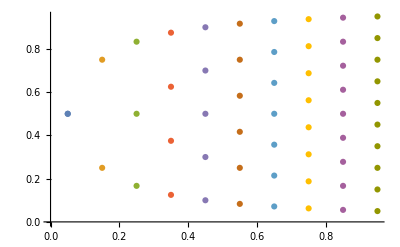

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

```mathematica
n=10;
tab=Table[{t0,t1},{t0,f[n]},{t1,f[n*t0+1/2]}]
ListPlot[tab]
```

```mathematica
(*変数逆距離重みに使っている重みに変更しては？*)
```

```mathematica
Ps=Table[{px[i],py[i],pz[i]},{i,0,11,1}];
tmp=Limit[Limit[Cross[MyinterpQuadIDW12Dt0[Ps,t0,t1],MyinterpQuadIDW12Dt1[Ps,t0,t1]],{t1->1/2}],{t0->0}]
```

{0,0,0}

```mathematica
tmp=FullSimplify@Limit[
Cross[
MyinterpQuadIDW12Dt0[Ps,t0,t1],
MyinterpQuadIDW12Dt1[Ps,t0,t1]],{t0->0}]
```

$Aborted

```mathematica
t0微分のt0->0
```

```mathematica
Ps=Table[P[i],{i,0,11,1}];
tmp=FullSimplify@Limit[MyinterpQuadIDW12Dt0[Ps,t0,t1],{t0->0}]
```

1/4 (-P[0]+(-1+t1+2 t1^2) P[1]+(-2+t1) (-1+2 t1) P[2]+(2+t1+t1^2) P[3]-4 (1+(-1+t1) t1) P[4]+(4+(-3+t1) t1) P[5]-t1^2 P[8]-t1 P[9]+(-1+t1) P[10]-(-1+t1)^2 P[11])

```mathematica
T2=.5;

approx=tmp/.{t1->T2};

eps=10^-15;
full=FullSimplify[MyinterpQuadIDW12Dt0[Ps,eps,T2]];


FullSimplify[full-approx]
```

0.+4.996×10^-16 P[0]-1.875×10^-16 P[1]-1.875×10^-16 P[2]-1.11022×10^-16 P[3]-4.44089×10^-16 P[4]-1.11022×10^-16 P[5]-6.25×10^-17 P[6]-6.25×10^-17 P[7]+9.02056×10^-17 P[8]+3.05311×10^-16 P[9]+3.05311×10^-16 P[10]+9.02056×10^-17 P[11]

```mathematica
t0微分のt0->1
```

```mathematica
tmp=Collect[Simplify@Limit[MyinterpQuadIDW12Dt0[Ps,t0,t1],{t0->1}],Ps,FullSimplify]
T2=.5;
approx=tmp/.{t1->T2};
eps=10^-6;
full=FullSimplify[MyinterpQuadIDW12Dt0[Table[P[i],{i,0,11,1}],1-eps,T2]];
FullSimplify[full-approx]
```

(3/4+t1-t1^2) P[0]+1/4 (-1+t1) (-1+2 t1) P[1]+1/4 t1 (-1+2 t1) P[2]+1/4 (-1+t1) P[3]+(-3/4+t1-t1^2) P[4]-1/4 t1 P[5]+1/4 t1 (-3+2 t1) P[6]+1/4 (-1+t1) (1+2 t1) P[7]+1/4 t1 P[8]+1/4 (1-t1) P[11]

0.-5.74998×10^-6 P[0]-1.12499×10^-6 P[1]-1.12499×10^-6 P[2]+4.74998×10^-6 P[3]-4.74998×10^-6 P[4]+4.74998×10^-6 P[5]+1.37499×10^-6 P[6]+1.37499×10^-6 P[7]-7.49997×10^-7 P[8]+9.99994×10^-7 P[9]+9.99994×10^-7 P[10]-7.49997×10^-7 P[11]

```mathematica
t1微分のt0->0
```

```mathematica
tmp=Collect[Simplify@Limit[MyinterpQuadIDW12Dt1[Ps,t0,t1],{t0->0}],Ps,FullSimplify]
T2=.5;
approx=tmp/.{t1->T2};
eps=10^-6;
full=FullSimplify[MyinterpQuadIDW12Dt1[Table[P[i],{i,0,11,1}],1-eps,T2]];
FullSimplify[full-approx]
```

0

0.+2.50002×10^-7 P[1]-2.50002×10^-7 P[2]+1. P[3]-1. P[5]+2.49999×10^-7 P[6]-2.49999×10^-7 P[7]-2.5×10^-7 P[8]-9.99996×10^-13 P[9]+9.99996×10^-13 P[10]+2.5×10^-7 P[11]

```mathematica
t1微分のt0->1
```

```mathematica
tmp=Collect[Simplify@Limit[MyinterpQuadIDW12Dt1[Ps,t0,t1],{t0->1}],Ps,FullSimplify]
T2=.5;
approx=tmp/.{t1->T2};
eps=10^-6;
full=FullSimplify[MyinterpQuadIDW12Dt1[Table[P[i],{i,0,11,1}],1-eps,T2]];
FullSimplify[full-approx]
```

```mathematica
t1微分のt1->1
```

```mathematica
tmp=Collect[Simplify@Limit[MyinterpQuadIDW12Dt1[Ps,t0,t1],{t1->1}],Ps,FullSimplify]
T=.5;
approx=tmp/.{t0->T};
eps=10^-6;
full=FullSimplify[MyinterpQuadIDW12Dt1[Table[P[i],{i,0,11,1}],T,1-eps]];
FullSimplify[full-approx]
```

1/4 (5-2 t0) t0 P[1]+1/4 t0 (-1+2 t0) P[2]-3/4 (-1+t0) t0 P[3]+1/4 t0 (-4+3 t0) P[4]-1/4 t0 (1+2 t0) P[5]+1/4 t0^2 P[7]+1/2 (-1+t0) t0 P[8]-1/4 t0 P[9]-1/4 (-1+t0) t0 P[10]

0.-2.49999×10^-7 P[0]-1.375×10^-6 P[1]-3.75×10^-7 P[2]+1.375×10^-6 P[3]+9.99998×10^-7 P[4]-1.125×10^-6 P[5]+2.49999×10^-7 P[6]-2.5×10^-7 P[7]+2.49999×10^-7 P[8]+3.74999×10^-7 P[9]-1.25×10^-7 P[10]+2.49999×10^-7 P[11]

```mathematica
FullSimplify@Limit[MyinterpQuadIDW12Dt0[Table[P[i],{i,0,11,1}],t0,t1],{t0->1}]
FullSimplify@Limit[MyinterpQuadIDW12Dt0[Table[P[i],{i,0,11,1}],t0,t1],{t1->1}]
FullSimplify@Limit[MyinterpQuadIDW12Dt0[Table[P[i],{i,0,11,1}],t0,t1],{t0->0}]
FullSimplify@Limit[MyinterpQuadIDW12Dt0[Table[P[i],{i,0,11,1}],t0,t1],{t1->0}]
```

1/4 ((3-4 (-1+t1) t1) P[0]+P[1]-P[3]-3 P[4]-P[7]+t1 ((-3+2 t1) P[1]-P[2]+P[3]+4 P[4]-P[5]-3 P[6]-P[7]+2 t1 (P[2]-2 P[4]+P[6]+P[7])+P[8]-P[11])+P[11])

1/4 ((-1+2 t0) P[0]+2 P[1]-P[2]+4 P[3]-4 P[4]+2 P[5]-P[8]-P[9]+2 t0 (-2 P[1]+P[2]-2 P[5]+P[8]+P[9]))

1/4 (-P[0]+(-1+t1+2 t1^2) P[1]+(-2+t1) (-1+2 t1) P[2]+(2+t1+t1^2) P[3]-4 (1+(-1+t1) t1) P[4]+(4+(-3+t1) t1) P[5]-t1^2 P[8]-t1 P[9]+(-1+t1) P[10]-(-1+t1)^2 P[11])

1/4 ((-1+2 t0) P[0]-P[1]+2 P[2]+2 P[3]-4 P[4]+4 P[5]-P[10]-P[11]+2 t0 (P[1]-2 P[2]-2 P[3]+P[10]+P[11]))

0

```mathematica
MyinterpQuadIDW12Dt0[ps,0,1]
MyinterpQuadIDW12Dt0[ps,0,0]
MyinterpQuadIDW12Dt0[ps,1,0]
MyinterpQuadIDW12Dt0[ps,1,1]
```

{2.84192,-0.502848,0.09262}

{1.48698,-1.09122,2.82386}

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

{Indeterminate,Indeterminate,Indeterminate}

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

{Indeterminate,Indeterminate,Indeterminate}

```mathematica
MyinterpQuadIDW12Dt1[ps,0,1]
MyinterpQuadIDW12Dt1[ps,0,0]
MyinterpQuadIDW12Dt1[ps,1,0]
MyinterpQuadIDW12Dt1[ps,1,1]
```

{0.,0.,0.}

{0.,0.,0.}

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

{Indeterminate,Indeterminate,Indeterminate}

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

{Indeterminate,Indeterminate,Indeterminate}

```mathematica
Limit[FullSimplify[Coefficient[MyinterpQuadIDW12Dt0[ps,t0,t1],ps]],{t0->0}]
Limit[FullSimplify[Coefficient[MyinterpQuadIDW12Dt0[ps,t0,t1],ps]],{t1->1}]
```

{-1/4,1/4 (-1+t1+2 t1^2),1/4 (2-5 t1+2 t1^2),1/4 (2+t1+t1^2),-1-(-1+t1) t1,1/4 (4+(-3+t1) t1),0,0,-t1^2/4,-t1/4,1/4 (-1+t1),-1/4 (-1+t1)^2}

{1/4 (-1+2 t0),1/2-t0,1/4 (-1+2 t0),1,-1,1/2-t0,0,0,1/4 (-1+2 t0),1/4 (-1+2 t0),0,0}

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
e=10^-7;
Manipulate[
Show[
{ParametricPlot3D[MyinterpQuadIDW12[ps,t0,t1],{t0,0,1},{t1,0,1},PlotStyle->Opacity[0.5]],
ParametricPlot3D[MyinterpQuadIDW12[ps,t0,t1],{t0,0,maxt0},{t1,0,maxt1},PlotStyle->Red],
ListPointPlot3D[{ps}]},
PlotRange->All]
,{maxt0,e,1,0.1},{maxt1,e,1,0.1}]
```

### データ

```mathematica
tab ={{{5.877850,6.881910,4.253250},{2.732670,9.619380,0.000000},{0.000000,8.506510,5.257310},{4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{3.090170,8.090170,5.000000},{4.253250,5.877850,6.881910},{6.937800,7.020460,1.606220},{5.257310,8.506510,0.000000},{0.000000,10.000000,0.000000},{-1.624600,9.510570,2.628660},{1.606220,6.937800,7.020460}},{{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,4.253250},{-2.732670,9.619380,0.000000},{-6.937800,7.020460,1.606220},{-4.338890,8.626680,2.598920},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,-2.598920},{-8.506510,5.257310,0.000000},{-8.090170,5.000000,3.090170},{-3.090170,8.090170,5.000000},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,-2.598920}},{{-8.626680,-2.598920,4.338890},{-5.257310,0.000000,8.506510},{-8.626680,2.598920,4.338890},{-7.020460,-1.606220,6.937800},{-7.020460,1.606220,6.937800},{-8.506510,0.000000,5.257310},{-9.619380,0.000000,2.732670},{-6.881910,-4.253250,5.877850},{-5.000000,-3.090170,8.090170},{-5.000000,3.090170,8.090170},{-6.881910,4.253250,5.877850},{-9.619380,0.000000,2.732670}},{{-2.598920,-4.338890,8.626680},{1.606220,-6.937800,7.020460},{2.628660,-1.624600,9.510570},{0.000000,-5.257310,8.506510},{2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{-2.628660,-1.624600,9.510570},{-1.606220,-6.937800,7.020460},{-1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000}},{{7.020460,1.606220,6.937800},{5.877850,6.881910,4.253250},{2.598920,4.338890,8.626680},{6.881910,4.253250,5.877850},{4.253250,5.877850,6.881910},{5.000000,3.090170,8.090170},{5.257310,0.000000,8.506510},{8.626680,2.598920,4.338890},{8.090170,5.000000,3.090170},{3.090170,8.090170,5.000000},{1.606220,6.937800,7.020460},{2.628660,1.624600,9.510570}},{{8.626680,-2.598920,4.338890},{9.510570,2.628660,1.624600},{7.020460,1.606220,6.937800},{9.619380,0.000000,2.732670},{8.626680,2.598920,4.338890},{8.506510,0.000000,5.257310},{7.020460,-1.606220,6.937800},{9.510570,-2.628660,1.624600},{10.000000,0.000000,0.000000},{8.090170,5.000000,3.090170},{6.881910,4.253250,5.877850},{7.020460,-1.606220,6.937800}},{{7.020460,-1.606220,6.937800},{9.510570,-2.628660,1.624600},{8.626680,2.598920,4.338890},{8.626680,-2.598920,4.338890},{9.619380,0.000000,2.732670},{8.506510,0.000000,5.257310},{7.020460,1.606220,6.937800},{6.881910,-4.253250,5.877850},{8.090170,-5.000000,3.090170},{10.000000,0.000000,0.000000},{9.510570,2.628660,1.624600},{7.020460,1.606220,6.937800}},{{2.598920,-4.338890,8.626680},{5.877850,-6.881910,4.253250},{7.020460,-1.606220,6.937800},{4.253250,-5.877850,6.881910},{6.881910,-4.253250,5.877850},{5.000000,-3.090170,8.090170},{2.628660,-1.624600,9.510570},{1.606220,-6.937800,7.020460},{3.090170,-8.090170,5.000000},{8.090170,-5.000000,3.090170},{8.626680,-2.598920,4.338890},{5.257310,0.000000,8.506510}},{{-2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{2.598920,-4.338890,8.626680},{-1.606220,-6.937800,7.020460},{1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{0.000000,-2.732670,9.619380},{-4.253250,-5.877850,6.881910},{-3.090170,-8.090170,5.000000},{3.090170,-8.090170,5.000000},{4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380}},{{-6.937800,-7.020460,-1.606220},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,2.598920},{-4.338890,-8.626680,-2.598920},{-2.732670,-9.619380,0.000000},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,-4.253250},{-3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,2.628660},{-6.937800,-7.020460,1.606220}},{{7.020460,-1.606220,-6.937800},{5.877850,-6.881910,-4.253250},{2.598920,-4.338890,-8.626680},{6.881910,-4.253250,-5.877850},{4.253250,-5.877850,-6.881910},{5.000000,-3.090170,-8.090170},{5.257310,0.000000,-8.506510},{8.626680,-2.598920,-4.338890},{8.090170,-5.000000,-3.090170},{3.090170,-8.090170,-5.000000},{1.606220,-6.937800,-7.020460},{2.628660,-1.624600,-9.510570}},{{-2.598920,-4.338890,-8.626680},{2.628660,-1.624600,-9.510570},{1.606220,-6.937800,-7.020460},{0.000000,-2.732670,-9.619380},{2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{-1.606220,-6.937800,-7.020460},{-2.628660,-1.624600,-9.510570},{0.000000,0.000000,-10.000000},{5.000000,-3.090170,-8.090170},{4.253250,-5.877850,-6.881910},{-1.606220,-6.937800,-7.020460}},{{-1.606220,-6.937800,-7.020460},{-2.628660,-1.624600,-9.510570},{2.598920,-4.338890,-8.626680},{-2.598920,-4.338890,-8.626680},{0.000000,-2.732670,-9.619380},{0.000000,-5.257310,-8.506510},{1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{-5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000},{2.628660,-1.624600,-9.510570},{1.606220,-6.937800,-7.020460}},{{-9.619380,0.000000,-2.732670},{-6.881910,4.253250,-5.877850},{-7.020460,-1.606220,-6.937800},{-8.626680,2.598920,-4.338890},{-7.020460,1.606220,-6.937800},{-8.506510,0.000000,-5.257310},{-8.626680,-2.598920,-4.338890},{-9.510570,2.628660,-1.624600},{-8.090170,5.000000,-3.090170},{-5.000000,3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{-8.626680,-2.598920,-4.338890}},{{4.338890,8.626680,2.598920},{6.937800,7.020460,-1.606220},{1.624600,9.510570,-2.628660},{5.257310,8.506510,0.000000},{4.338890,8.626680,-2.598920},{2.732670,9.619380,0.000000},{1.624600,9.510570,2.628660},{6.937800,7.020460,1.606220},{6.937800,7.020460,1.606220},{5.877850,6.881910,-4.253250},{3.090170,8.090170,-5.000000},{0.000000,10.000000,0.000000}},{{8.626680,2.598920,-4.338890},{4.253250,5.877850,-6.881910},{6.937800,7.020460,-1.606220},{6.881910,4.253250,-5.877850},{5.877850,6.881910,-4.253250},{8.090170,5.000000,-3.090170},{9.510570,2.628660,-1.624600},{7.020460,1.606220,-6.937800},{5.000000,3.090170,-8.090170},{3.090170,8.090170,-5.000000},{4.338890,8.626680,-2.598920},{8.506510,5.257310,0.000000}},{{-9.619380,0.000000,2.732670},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,1.624600},{-9.510570,2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,1.624600},{-8.626680,2.598920,4.338890},{-8.090170,5.000000,3.090170},{-8.090170,5.000000,-3.090170},{-8.626680,2.598920,-4.338890},{-9.510570,-2.628660,-1.624600}},{{-8.626680,2.598920,-4.338890},{-7.020460,-1.606220,-6.937800},{-9.510570,-2.628660,-1.624600},{-8.506510,0.000000,-5.257310},{-8.626680,-2.598920,-4.338890},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,-1.624600},{-7.020460,1.606220,-6.937800},{-7.020460,1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-8.090170,-5.000000,-3.090170},{-10.000000,0.000000,0.000000}},{{-1.606220,-6.937800,7.020460},{-6.881910,-4.253250,5.877850},{-4.338890,-8.626680,2.598920},{-4.253250,-5.877850,6.881910},{-5.877850,-6.881910,4.253250},{-3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{-2.598920,-4.338890,8.626680},{-5.000000,-3.090170,8.090170},{-8.090170,-5.000000,3.090170},{-6.937800,-7.020460,1.606220},{-1.624600,-9.510570,2.628660}},{{-4.338890,-8.626680,-2.598920},{-6.881910,-4.253250,-5.877850},{-1.606220,-6.937800,-7.020460},{-5.877850,-6.881910,-4.253250},{-4.253250,-5.877850,-6.881910},{-3.090170,-8.090170,-5.000000},{-1.624600,-9.510570,-2.628660},{-6.937800,-7.020460,-1.606220},{-8.090170,-5.000000,-3.090170},{-5.000000,-3.090170,-8.090170},{-2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310}},{{-4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{-1.624600,9.510570,2.628660},{-1.606220,6.937800,7.020460},{0.000000,8.506510,5.257310},{-3.090170,8.090170,5.000000},{-5.877850,6.881910,4.253250},{-2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{3.090170,8.090170,5.000000},{1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920}},{{-9.510570,2.628660,1.624600},{-7.020460,1.606220,6.937800},{-5.877850,6.881910,4.253250},{-8.626680,2.598920,4.338890},{-6.881910,4.253250,5.877850},{-8.090170,5.000000,3.090170},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,2.732670},{-8.506510,0.000000,5.257310},{-5.000000,3.090170,8.090170},{-4.253250,5.877850,6.881910},{-6.937800,7.020460,1.606220}},{{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{-2.732670,9.619380,0.000000},{-1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-5.257310,8.506510,0.000000},{-3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{2.732670,9.619380,0.000000}},{{-5.257310,8.506510,0.000000},{0.000000,10.000000,0.000000},{-3.090170,8.090170,-5.000000},{-2.732670,9.619380,0.000000},{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-6.937800,7.020460,-1.606220},{-4.338890,8.626680,2.598920},{-1.624600,9.510570,2.628660},{1.624600,9.510570,-2.628660},{0.000000,8.506510,-5.257310},{-5.877850,6.881910,-4.253250}},{{-6.937800,7.020460,1.606220},{-8.626680,2.598920,4.338890},{-4.253250,5.877850,6.881910},{-8.090170,5.000000,3.090170},{-6.881910,4.253250,5.877850},{-5.877850,6.881910,4.253250},{-4.338890,8.626680,2.598920},{-8.506510,5.257310,0.000000},{-9.510570,2.628660,1.624600},{-7.020460,1.606220,6.937800},{-5.000000,3.090170,8.090170},{-3.090170,8.090170,5.000000}},{{-8.626680,-2.598920,-4.338890},{-9.510570,2.628660,-1.624600},{-7.020460,1.606220,-6.937800},{-9.619380,0.000000,-2.732670},{-8.626680,2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-7.020460,-1.606220,-6.937800},{-9.510570,-2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,-3.090170},{-6.881910,4.253250,-5.877850},{-7.020460,-1.606220,-6.937800}},{{-8.506510,5.257310,0.000000},{-4.338890,8.626680,-2.598920},{-6.881910,4.253250,-5.877850},{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,-4.253250},{-8.090170,5.000000,-3.090170},{-9.510570,2.628660,-1.624600},{-6.937800,7.020460,1.606220},{-5.257310,8.506510,0.000000},{-3.090170,8.090170,-5.000000},{-4.253250,5.877850,-6.881910},{-8.626680,2.598920,-4.338890}},{{-5.257310,8.506510,0.000000},{-8.090170,5.000000,-3.090170},{-8.090170,5.000000,3.090170},{-6.937800,7.020460,-1.606220},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,1.606220},{-4.338890,8.626680,2.598920},{-4.338890,8.626680,-2.598920},{-5.877850,6.881910,-4.253250},{-9.510570,2.628660,-1.624600},{-9.510570,2.628660,1.624600},{-5.877850,6.881910,4.253250}},{{-3.090170,8.090170,-5.000000},{-5.000000,3.090170,-8.090170},{-8.090170,5.000000,-3.090170},{-4.253250,5.877850,-6.881910},{-6.881910,4.253250,-5.877850},{-5.877850,6.881910,-4.253250},{-4.338890,8.626680,-2.598920},{-1.606220,6.937800,-7.020460},{-2.598920,4.338890,-8.626680},{-7.020460,1.606220,-6.937800},{-8.626680,2.598920,-4.338890},{-6.937800,7.020460,-1.606220}},{{-3.090170,8.090170,-5.000000},{3.090170,8.090170,-5.000000},{0.000000,5.257310,-8.506510},{0.000000,8.506510,-5.257310},{1.606220,6.937800,-7.020460},{-1.606220,6.937800,-7.020460},{-4.253250,5.877850,-6.881910},{-1.624600,9.510570,-2.628660},{1.624600,9.510570,-2.628660},{4.253250,5.877850,-6.881910},{2.598920,4.338890,-8.626680},{-2.598920,4.338890,-8.626680}},{{0.000000,8.506510,5.257310},{2.732670,9.619380,0.000000},{-2.732670,9.619380,0.000000},{1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{-1.624600,9.510570,2.628660},{-3.090170,8.090170,5.000000},{3.090170,8.090170,5.000000},{4.338890,8.626680,2.598920},{1.624600,9.510570,-2.628660},{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,2.598920}},{{9.619380,0.000000,2.732670},{6.881910,4.253250,5.877850},{7.020460,-1.606220,6.937800},{8.626680,2.598920,4.338890},{7.020460,1.606220,6.937800},{8.506510,0.000000,5.257310},{8.626680,-2.598920,4.338890},{9.510570,2.628660,1.624600},{8.090170,5.000000,3.090170},{5.000000,3.090170,8.090170},{5.257310,0.000000,8.506510},{8.626680,-2.598920,4.338890}},{{3.090170,8.090170,5.000000},{8.090170,5.000000,3.090170},{5.257310,8.506510,0.000000},{5.877850,6.881910,4.253250},{6.937800,7.020460,1.606220},{4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{4.253250,5.877850,6.881910},{6.881910,4.253250,5.877850},{8.506510,5.257310,0.000000},{6.937800,7.020460,-1.606220},{2.732670,9.619380,0.000000}},{{9.510570,-2.628660,-1.624600},{8.626680,2.598920,-4.338890},{9.510570,2.628660,1.624600},{9.619380,0.000000,-2.732670},{9.510570,2.628660,-1.624600},{10.000000,0.000000,0.000000},{9.510570,-2.628660,1.624600},{8.626680,-2.598920,-4.338890},{8.506510,0.000000,-5.257310},{8.090170,5.000000,-3.090170},{8.506510,5.257310,0.000000},{9.619380,0.000000,2.732670}},{{8.090170,5.000000,3.090170},{8.090170,5.000000,-3.090170},{5.257310,8.506510,0.000000},{8.506510,5.257310,0.000000},{6.937800,7.020460,-1.606220},{6.937800,7.020460,1.606220},{5.877850,6.881910,4.253250},{9.510570,2.628660,1.624600},{9.510570,2.628660,-1.624600},{5.877850,6.881910,-4.253250},{4.338890,8.626680,-2.598920},{4.338890,8.626680,2.598920}},{{5.257310,8.506510,0.000000},{8.090170,5.000000,-3.090170},{3.090170,8.090170,-5.000000},{6.937800,7.020460,-1.606220},{5.877850,6.881910,-4.253250},{4.338890,8.626680,-2.598920},{2.732670,9.619380,0.000000},{6.937800,7.020460,1.606220},{8.506510,5.257310,0.000000},{6.881910,4.253250,-5.877850},{4.253250,5.877850,-6.881910},{1.624600,9.510570,-2.628660}},{{0.000000,10.000000,0.000000},{3.090170,8.090170,-5.000000},{-3.090170,8.090170,-5.000000},{1.624600,9.510570,-2.628660},{0.000000,8.506510,-5.257310},{-1.624600,9.510570,-2.628660},{-2.732670,9.619380,0.000000},{2.732670,9.619380,0.000000},{4.338890,8.626680,-2.598920},{1.606220,6.937800,-7.020460},{-1.606220,6.937800,-7.020460},{-4.338890,8.626680,-2.598920}},{{0.000000,5.257310,-8.506510},{3.090170,8.090170,-5.000000},{5.000000,3.090170,-8.090170},{1.606220,6.937800,-7.020460},{4.253250,5.877850,-6.881910},{2.598920,4.338890,-8.626680},{0.000000,2.732670,-9.619380},{-1.606220,6.937800,-7.020460},{0.000000,8.506510,-5.257310},{5.877850,6.881910,-4.253250},{6.881910,4.253250,-5.877850},{2.628660,1.624600,-9.510570}},{{-5.877850,-6.881910,4.253250},{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310},{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660},{-3.090170,-8.090170,5.000000},{-4.253250,-5.877850,6.881910},{-6.937800,-7.020460,1.606220},{-5.257310,-8.506510,0.000000},{0.000000,-10.000000,0.000000},{1.624600,-9.510570,2.628660},{-1.606220,-6.937800,7.020460}},{{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,5.000000},{-8.090170,-5.000000,3.090170},{-4.338890,-8.626680,2.598920},{-5.877850,-6.881910,4.253250},{-6.937800,-7.020460,1.606220},{-6.937800,-7.020460,-1.606220},{-2.732670,-9.619380,0.000000},{-1.624600,-9.510570,2.628660},{-4.253250,-5.877850,6.881910},{-6.881910,-4.253250,5.877850},{-8.506510,-5.257310,0.000000}},{{0.000000,-10.000000,0.000000},{3.090170,-8.090170,5.000000},{-3.090170,-8.090170,5.000000},{1.624600,-9.510570,2.628660},{0.000000,-8.506510,5.257310},{-1.624600,-9.510570,2.628660},{-2.732670,-9.619380,0.000000},{2.732670,-9.619380,0.000000},{4.338890,-8.626680,2.598920},{1.606220,-6.937800,7.020460},{-1.606220,-6.937800,7.020460},{-4.338890,-8.626680,2.598920}},{{-4.253250,-5.877850,-6.881910},{1.606220,-6.937800,-7.020460},{-1.624600,-9.510570,-2.628660},{-1.606220,-6.937800,-7.020460},{0.000000,-8.506510,-5.257310},{-3.090170,-8.090170,-5.000000},{-5.877850,-6.881910,-4.253250},{-2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{3.090170,-8.090170,-5.000000},{1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,-2.598920}},{{-4.338890,-8.626680,-2.598920},{-1.606220,-6.937800,-7.020460},{1.624600,-9.510570,-2.628660},{-3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{-1.624600,-9.510570,-2.628660},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,-4.253250},{-4.253250,-5.877850,-6.881910},{1.606220,-6.937800,-7.020460},{3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000}},{{0.000000,-5.257310,-8.506510},{-3.090170,-8.090170,-5.000000},{-5.000000,-3.090170,-8.090170},{-1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{-2.598920,-4.338890,-8.626680},{0.000000,-2.732670,-9.619380},{1.606220,-6.937800,-7.020460},{0.000000,-8.506510,-5.257310},{-5.877850,-6.881910,-4.253250},{-6.881910,-4.253250,-5.877850},{-2.628660,-1.624600,-9.510570}},{{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,1.606220},{-9.510570,-2.628660,-1.624600},{-6.937800,-7.020460,-1.606220},{-8.506510,-5.257310,0.000000},{-8.090170,-5.000000,-3.090170},{-6.881910,-4.253250,-5.877850},{-4.338890,-8.626680,-2.598920},{-5.257310,-8.506510,0.000000},{-8.090170,-5.000000,3.090170},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,-4.338890}},{{-5.257310,-8.506510,0.000000},{-8.090170,-5.000000,-3.090170},{-3.090170,-8.090170,-5.000000},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,-4.253250},{-4.338890,-8.626680,-2.598920},{-2.732670,-9.619380,0.000000},{-6.937800,-7.020460,1.606220},{-8.506510,-5.257310,0.000000},{-6.881910,-4.253250,-5.877850},{-4.253250,-5.877850,-6.881910},{-1.624600,-9.510570,-2.628660}},{{-8.090170,-5.000000,3.090170},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,-3.090170},{-9.510570,-2.628660,1.624600},{-9.510570,-2.628660,-1.624600},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,1.606220},{-8.626680,-2.598920,4.338890},{-9.619380,0.000000,2.732670},{-9.619380,0.000000,-2.732670},{-8.626680,-2.598920,-4.338890},{-6.937800,-7.020460,-1.606220}},{{-8.506510,0.000000,5.257310},{-8.090170,-5.000000,3.090170},{-5.000000,-3.090170,8.090170},{-8.626680,-2.598920,4.338890},{-6.881910,-4.253250,5.877850},{-7.020460,-1.606220,6.937800},{-7.020460,1.606220,6.937800},{-9.619380,0.000000,2.732670},{-9.510570,-2.628660,1.624600},{-5.877850,-6.881910,4.253250},{-4.253250,-5.877850,6.881910},{-5.257310,0.000000,8.506510}},{{5.877850,-6.881910,4.253250},{6.937800,-7.020460,-1.606220},{9.510570,-2.628660,1.624600},{6.937800,-7.020460,1.606220},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,3.090170},{6.881910,-4.253250,5.877850},{4.338890,-8.626680,2.598920},{5.257310,-8.506510,0.000000},{8.090170,-5.000000,-3.090170},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,4.338890}},{{-1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380},{1.606220,-6.937800,7.020460},{2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{-2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{3.090170,-8.090170,5.000000},{5.000000,-3.090170,8.090170},{2.628660,-1.624600,9.510570},{-2.598920,-4.338890,8.626680}},{{8.090170,-5.000000,-3.090170},{10.000000,0.000000,0.000000},{8.090170,-5.000000,3.090170},{9.510570,-2.628660,-1.624600},{9.510570,-2.628660,1.624600},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,-1.606220},{8.626680,-2.598920,-4.338890},{9.619380,0.000000,-2.732670},{9.619380,0.000000,2.732670},{8.626680,-2.598920,4.338890},{6.937800,-7.020460,1.606220}},{{0.000000,-2.732670,-9.619380},{4.253250,-5.877850,-6.881910},{-1.606220,-6.937800,-7.020460},{2.598920,-4.338890,-8.626680},{1.606220,-6.937800,-7.020460},{0.000000,-5.257310,-8.506510},{-2.598920,-4.338890,-8.626680},{2.628660,-1.624600,-9.510570},{5.000000,-3.090170,-8.090170},{3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{-2.598920,-4.338890,-8.626680}},{{8.090170,-5.000000,3.090170},{3.090170,-8.090170,5.000000},{5.257310,-8.506510,0.000000},{5.877850,-6.881910,4.253250},{4.338890,-8.626680,2.598920},{6.937800,-7.020460,1.606220},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,5.877850},{4.253250,-5.877850,6.881910},{1.624600,-9.510570,2.628660},{2.732670,-9.619380,0.000000},{6.937800,-7.020460,-1.606220}},{{0.000000,-8.506510,5.257310},{2.732670,-9.619380,0.000000},{5.877850,-6.881910,4.253250},{1.624600,-9.510570,2.628660},{4.338890,-8.626680,2.598920},{3.090170,-8.090170,5.000000},{1.606220,-6.937800,7.020460},{-1.624600,-9.510570,2.628660},{0.000000,-10.000000,0.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,1.606220},{4.253250,-5.877850,6.881910}},{{0.000000,-10.000000,0.000000},{3.090170,-8.090170,-5.000000},{5.257310,-8.506510,0.000000},{1.624600,-9.510570,-2.628660},{4.338890,-8.626680,-2.598920},{2.732670,-9.619380,0.000000},{1.624600,-9.510570,2.628660},{-1.624600,-9.510570,-2.628660},{0.000000,-8.506510,-5.257310},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,-1.606220},{4.338890,-8.626680,2.598920}},{{5.257310,-8.506510,0.000000},{3.090170,-8.090170,-5.000000},{8.090170,-5.000000,-3.090170},{4.338890,-8.626680,-2.598920},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,-1.606220},{6.937800,-7.020460,1.606220},{2.732670,-9.619380,0.000000},{1.624600,-9.510570,-2.628660},{4.253250,-5.877850,-6.881910},{6.881910,-4.253250,-5.877850},{8.506510,-5.257310,0.000000}},{{-3.090170,8.090170,5.000000},{-5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510},{-4.253250,5.877850,6.881910},{-2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460},{0.000000,8.506510,5.257310},{-5.877850,6.881910,4.253250},{-6.881910,4.253250,5.877850},{-2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{1.606220,6.937800,7.020460}},{{-4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380},{-5.257310,0.000000,8.506510},{-2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570},{-5.000000,-3.090170,8.090170},{-6.881910,-4.253250,5.877850},{-1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{0.000000,0.000000,10.000000},{-2.628660,1.624600,9.510570},{-7.020460,-1.606220,6.937800}},{{-5.000000,3.090170,8.090170},{0.000000,0.000000,10.000000},{0.000000,5.257310,8.506510},{-2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{-2.598920,4.338890,8.626680},{-4.253250,5.877850,6.881910},{-5.257310,0.000000,8.506510},{-2.628660,-1.624600,9.510570},{2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460}},{{6.881910,-4.253250,5.877850},{7.020460,1.606220,6.937800},{2.628660,-1.624600,9.510570},{7.020460,-1.606220,6.937800},{5.257310,0.000000,8.506510},{5.000000,-3.090170,8.090170},{4.253250,-5.877850,6.881910},{8.626680,-2.598920,4.338890},{8.506510,0.000000,5.257310},{5.000000,3.090170,8.090170},{2.628660,1.624600,9.510570},{2.598920,-4.338890,8.626680}},{{0.000000,0.000000,10.000000},{5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510},{2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{0.000000,2.732670,9.619380},{-2.628660,1.624600,9.510570},{2.628660,-1.624600,9.510570},{5.257310,0.000000,8.506510},{4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{-2.598920,4.338890,8.626680}},{{0.000000,5.257310,8.506510},{5.000000,3.090170,8.090170},{3.090170,8.090170,5.000000},{2.598920,4.338890,8.626680},{4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{-1.606220,6.937800,7.020460},{0.000000,2.732670,9.619380},{2.628660,1.624600,9.510570},{6.881910,4.253250,5.877850},{5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310}},{{-2.598920,-4.338890,8.626680},{-2.628660,1.624600,9.510570},{-7.020460,-1.606220,6.937800},{-2.628660,-1.624600,9.510570},{-5.257310,0.000000,8.506510},{-5.000000,-3.090170,8.090170},{-4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380},{0.000000,0.000000,10.000000},{-5.000000,3.090170,8.090170},{-7.020460,1.606220,6.937800},{-6.881910,-4.253250,5.877850}},{{0.000000,-5.257310,8.506510},{-5.000000,-3.090170,8.090170},{-3.090170,-8.090170,5.000000},{-2.598920,-4.338890,8.626680},{-4.253250,-5.877850,6.881910},{-1.606220,-6.937800,7.020460},{1.606220,-6.937800,7.020460},{0.000000,-2.732670,9.619380},{-2.628660,-1.624600,9.510570},{-6.881910,-4.253250,5.877850},{-5.877850,-6.881910,4.253250},{0.000000,-8.506510,5.257310}},{{7.020460,-1.606220,6.937800},{2.628660,1.624600,9.510570},{2.598920,-4.338890,8.626680},{5.257310,0.000000,8.506510},{2.628660,-1.624600,9.510570},{5.000000,-3.090170,8.090170},{6.881910,-4.253250,5.877850},{7.020460,1.606220,6.937800},{5.000000,3.090170,8.090170},{0.000000,0.000000,10.000000},{0.000000,-2.732670,9.619380},{4.253250,-5.877850,6.881910}},{{8.506510,0.000000,5.257310},{5.000000,-3.090170,8.090170},{8.090170,-5.000000,3.090170},{7.020460,-1.606220,6.937800},{6.881910,-4.253250,5.877850},{8.626680,-2.598920,4.338890},{9.619380,0.000000,2.732670},{7.020460,1.606220,6.937800},{5.257310,0.000000,8.506510},{4.253250,-5.877850,6.881910},{5.877850,-6.881910,4.253250},{9.510570,-2.628660,1.624600}},{{-2.628660,1.624600,-9.510570},{2.598920,4.338890,-8.626680},{2.628660,-1.624600,-9.510570},{0.000000,2.732670,-9.619380},{2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{-2.628660,-1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{5.000000,3.090170,-8.090170},{5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380}},{{-6.881910,-4.253250,-5.877850},{-7.020460,1.606220,-6.937800},{-2.628660,-1.624600,-9.510570},{-7.020460,-1.606220,-6.937800},{-5.257310,0.000000,-8.506510},{-5.000000,-3.090170,-8.090170},{-4.253250,-5.877850,-6.881910},{-8.626680,-2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-5.000000,3.090170,-8.090170},{-2.628660,1.624600,-9.510570},{-2.598920,-4.338890,-8.626680}},{{5.000000,3.090170,-8.090170},{5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000},{5.257310,0.000000,-8.506510},{2.628660,-1.624600,-9.510570},{2.628660,1.624600,-9.510570},{2.598920,4.338890,-8.626680},{7.020460,1.606220,-6.937800},{7.020460,-1.606220,-6.937800},{2.598920,-4.338890,-8.626680},{0.000000,-2.732670,-9.619380},{0.000000,2.732670,-9.619380}},{{8.506510,0.000000,-5.257310},{5.000000,3.090170,-8.090170},{8.090170,5.000000,-3.090170},{7.020460,1.606220,-6.937800},{6.881910,4.253250,-5.877850},{8.626680,2.598920,-4.338890},{9.619380,0.000000,-2.732670},{7.020460,-1.606220,-6.937800},{5.257310,0.000000,-8.506510},{4.253250,5.877850,-6.881910},{5.877850,6.881910,-4.253250},{9.510570,2.628660,-1.624600}},{{0.000000,0.000000,-10.000000},{-5.000000,3.090170,-8.090170},{0.000000,5.257310,-8.506510},{-2.628660,1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{0.000000,2.732670,-9.619380},{2.628660,1.624600,-9.510570},{-2.628660,-1.624600,-9.510570},{-5.257310,0.000000,-8.506510},{-4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{2.598920,4.338890,-8.626680}},{{-6.881910,4.253250,-5.877850},{-1.606220,6.937800,-7.020460},{-2.628660,1.624600,-9.510570},{-4.253250,5.877850,-6.881910},{-2.598920,4.338890,-8.626680},{-5.000000,3.090170,-8.090170},{-7.020460,1.606220,-6.937800},{-5.877850,6.881910,-4.253250},{-3.090170,8.090170,-5.000000},{0.000000,5.257310,-8.506510},{0.000000,2.732670,-9.619380},{-5.257310,0.000000,-8.506510}},{{8.090170,-5.000000,-3.090170},{5.000000,-3.090170,-8.090170},{8.506510,0.000000,-5.257310},{6.881910,-4.253250,-5.877850},{7.020460,-1.606220,-6.937800},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{5.877850,-6.881910,-4.253250},{4.253250,-5.877850,-6.881910},{5.257310,0.000000,-8.506510},{7.020460,1.606220,-6.937800},{9.619380,0.000000,-2.732670}},{{2.628660,-1.624600,-9.510570},{7.020460,1.606220,-6.937800},{6.881910,-4.253250,-5.877850},{5.257310,0.000000,-8.506510},{7.020460,-1.606220,-6.937800},{5.000000,-3.090170,-8.090170},{2.598920,-4.338890,-8.626680},{2.628660,1.624600,-9.510570},{5.000000,3.090170,-8.090170},{8.506510,0.000000,-5.257310},{8.626680,-2.598920,-4.338890},{4.253250,-5.877850,-6.881910}},{{-7.020460,-1.606220,-6.937800},{-2.628660,1.624600,-9.510570},{-2.598920,-4.338890,-8.626680},{-5.257310,0.000000,-8.506510},{-2.628660,-1.624600,-9.510570},{-5.000000,-3.090170,-8.090170},{-6.881910,-4.253250,-5.877850},{-7.020460,1.606220,-6.937800},{-5.000000,3.090170,-8.090170},{0.000000,0.000000,-10.000000},{0.000000,-2.732670,-9.619380},{-4.253250,-5.877850,-6.881910}},{{-8.506510,0.000000,-5.257310},{-5.000000,-3.090170,-8.090170},{-8.090170,-5.000000,-3.090170},{-7.020460,-1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-8.626680,-2.598920,-4.338890},{-9.619380,0.000000,-2.732670},{-7.020460,1.606220,-6.937800},{-5.257310,0.000000,-8.506510},{-4.253250,-5.877850,-6.881910},{-5.877850,-6.881910,-4.253250},{-9.510570,-2.628660,-1.624600}},{{9.619380,0.000000,-2.732670},{8.506510,5.257310,0.000000},{9.619380,0.000000,2.732670},{9.510570,2.628660,-1.624600},{9.510570,2.628660,1.624600},{10.000000,0.000000,0.000000},{9.510570,-2.628660,-1.624600},{8.626680,2.598920,-4.338890},{8.090170,5.000000,-3.090170},{8.090170,5.000000,3.090170},{8.626680,2.598920,4.338890},{9.510570,-2.628660,1.624600}},{{9.510570,-2.628660,1.624600},{8.626680,-2.598920,-4.338890},{9.510570,2.628660,-1.624600},{9.510570,-2.628660,-1.624600},{9.619380,0.000000,-2.732670},{10.000000,0.000000,0.000000},{9.619380,0.000000,2.732670},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,-3.090170},{8.506510,0.000000,-5.257310},{8.626680,2.598920,-4.338890},{9.510570,2.628660,1.624600}},{{-8.090170,5.000000,3.090170},{-10.000000,0.000000,0.000000},{-8.506510,0.000000,5.257310},{-9.510570,2.628660,1.624600},{-9.619380,0.000000,2.732670},{-8.626680,2.598920,4.338890},{-6.881910,4.253250,5.877850},{-8.506510,5.257310,0.000000},{-9.510570,2.628660,-1.624600},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,4.338890},{-7.020460,1.606220,6.937800}},{{-9.510570,-2.628660,-1.624600},{-8.626680,-2.598920,4.338890},{-9.510570,2.628660,1.624600},{-9.510570,-2.628660,1.624600},{-9.619380,0.000000,2.732670},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,-2.732670},{-8.506510,-5.257310,0.000000},{-8.090170,-5.000000,3.090170},{-8.506510,0.000000,5.257310},{-8.626680,2.598920,4.338890},{-9.510570,2.628660,-1.624600}},{{-3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{-5.257310,8.506510,0.000000},{-1.624600,9.510570,2.628660},{-2.732670,9.619380,0.000000},{-4.338890,8.626680,2.598920},{-5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310},{1.624600,9.510570,2.628660},{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-6.937800,7.020460,1.606220}},{{-6.881910,4.253250,5.877850},{-4.338890,8.626680,2.598920},{-8.506510,5.257310,0.000000},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,1.606220},{-8.090170,5.000000,3.090170},{-8.626680,2.598920,4.338890},{-4.253250,5.877850,6.881910},{-3.090170,8.090170,5.000000},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,-1.606220},{-9.510570,2.628660,1.624600}},{{-5.257310,8.506510,0.000000},{-8.090170,5.000000,3.090170},{-3.090170,8.090170,5.000000},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,4.253250},{-4.338890,8.626680,2.598920},{-2.732670,9.619380,0.000000},{-6.937800,7.020460,-1.606220},{-8.506510,5.257310,0.000000},{-6.881910,4.253250,5.877850},{-4.253250,5.877850,6.881910},{-1.624600,9.510570,2.628660}},{{-5.877850,6.881910,4.253250},{-6.937800,7.020460,-1.606220},{-9.510570,2.628660,1.624600},{-6.937800,7.020460,1.606220},{-8.506510,5.257310,0.000000},{-8.090170,5.000000,3.090170},{-6.881910,4.253250,5.877850},{-4.338890,8.626680,2.598920},{-5.257310,8.506510,0.000000},{-8.090170,5.000000,-3.090170},{-9.510570,2.628660,-1.624600},{-8.626680,2.598920,4.338890}},{{-6.937800,7.020460,-1.606220},{-1.624600,9.510570,-2.628660},{-4.253250,5.877850,-6.881910},{-4.338890,8.626680,-2.598920},{-3.090170,8.090170,-5.000000},{-5.877850,6.881910,-4.253250},{-8.090170,5.000000,-3.090170},{-5.257310,8.506510,0.000000},{-2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-1.606220,6.937800,-7.020460},{-6.881910,4.253250,-5.877850}},{{1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,2.628660},{-1.624600,9.510570,-2.628660},{-2.732670,9.619380,0.000000},{0.000000,10.000000,0.000000},{2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-3.090170,8.090170,-5.000000},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660}},{{-6.937800,7.020460,1.606220},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,-2.598920},{-4.338890,8.626680,2.598920},{-2.732670,9.619380,0.000000},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,4.253250},{-3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{-1.624600,9.510570,-2.628660},{-6.937800,7.020460,-1.606220}},{{-4.338890,8.626680,2.598920},{-1.624600,9.510570,-2.628660},{-6.937800,7.020460,-1.606220},{-2.732670,9.619380,0.000000},{-4.338890,8.626680,-2.598920},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,1.606220},{-1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{-3.090170,8.090170,-5.000000},{-5.877850,6.881910,-4.253250},{-6.937800,7.020460,1.606220}},{{-6.937800,7.020460,1.606220},{-2.732670,9.619380,0.000000},{-5.877850,6.881910,-4.253250},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,-2.598920},{-6.937800,7.020460,-1.606220},{-8.506510,5.257310,0.000000},{-4.338890,8.626680,2.598920},{-4.338890,8.626680,2.598920},{-1.624600,9.510570,-2.628660},{-3.090170,8.090170,-5.000000},{-8.090170,5.000000,-3.090170}},{{-4.338890,8.626680,2.598920},{-4.338890,8.626680,-2.598920},{-8.506510,5.257310,0.000000},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,-1.606220},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,4.253250},{-2.732670,9.619380,0.000000},{-2.732670,9.619380,0.000000},{-5.877850,6.881910,-4.253250},{-8.090170,5.000000,-3.090170},{-8.090170,5.000000,3.090170}},{{1.624600,9.510570,-2.628660},{-1.624600,9.510570,2.628660},{4.338890,8.626680,2.598920},{0.000000,10.000000,0.000000},{1.624600,9.510570,2.628660},{2.732670,9.619380,0.000000},{4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{-2.732670,9.619380,0.000000},{0.000000,8.506510,5.257310},{3.090170,8.090170,5.000000},{5.257310,8.506510,0.000000}},{{0.000000,8.506510,-5.257310},{2.732670,9.619380,0.000000},{5.877850,6.881910,-4.253250},{1.624600,9.510570,-2.628660},{4.338890,8.626680,-2.598920},{3.090170,8.090170,-5.000000},{1.606220,6.937800,-7.020460},{-1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{5.257310,8.506510,0.000000},{6.937800,7.020460,-1.606220},{4.253250,5.877850,-6.881910}},{{5.257310,8.506510,0.000000},{3.090170,8.090170,-5.000000},{0.000000,10.000000,0.000000},{4.338890,8.626680,-2.598920},{1.624600,9.510570,-2.628660},{2.732670,9.619380,0.000000},{4.338890,8.626680,2.598920},{6.937800,7.020460,-1.606220},{5.877850,6.881910,-4.253250},{0.000000,8.506510,-5.257310},{-1.624600,9.510570,-2.628660},{1.624600,9.510570,2.628660}},{{6.881910,4.253250,-5.877850},{4.338890,8.626680,-2.598920},{8.506510,5.257310,0.000000},{5.877850,6.881910,-4.253250},{6.937800,7.020460,-1.606220},{8.090170,5.000000,-3.090170},{8.626680,2.598920,-4.338890},{4.253250,5.877850,-6.881910},{3.090170,8.090170,-5.000000},{5.257310,8.506510,0.000000},{6.937800,7.020460,1.606220},{9.510570,2.628660,-1.624600}},{{4.338890,8.626680,-2.598920},{1.624600,9.510570,2.628660},{6.937800,7.020460,1.606220},{2.732670,9.619380,0.000000},{4.338890,8.626680,2.598920},{5.257310,8.506510,0.000000},{6.937800,7.020460,-1.606220},{1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{3.090170,8.090170,5.000000},{5.877850,6.881910,4.253250},{6.937800,7.020460,-1.606220}},{{8.506510,5.257310,0.000000},{4.338890,8.626680,2.598920},{6.881910,4.253250,5.877850},{6.937800,7.020460,1.606220},{5.877850,6.881910,4.253250},{8.090170,5.000000,3.090170},{9.510570,2.628660,1.624600},{6.937800,7.020460,-1.606220},{5.257310,8.506510,0.000000},{3.090170,8.090170,5.000000},{4.253250,5.877850,6.881910},{8.626680,2.598920,4.338890}},{{5.877850,6.881910,4.253250},{6.937800,7.020460,-1.606220},{2.732670,9.619380,0.000000},{6.937800,7.020460,1.606220},{5.257310,8.506510,0.000000},{4.338890,8.626680,2.598920},{3.090170,8.090170,5.000000},{8.090170,5.000000,3.090170},{8.506510,5.257310,0.000000},{4.338890,8.626680,-2.598920},{4.338890,8.626680,-2.598920},{1.624600,9.510570,2.628660}},{{5.877850,6.881910,-4.253250},{6.937800,7.020460,1.606220},{9.510570,2.628660,-1.624600},{6.937800,7.020460,-1.606220},{8.506510,5.257310,0.000000},{8.090170,5.000000,-3.090170},{6.881910,4.253250,-5.877850},{4.338890,8.626680,-2.598920},{5.257310,8.506510,0.000000},{8.090170,5.000000,3.090170},{9.510570,2.628660,1.624600},{8.626680,2.598920,-4.338890}},{{8.506510,5.257310,0.000000},{4.338890,8.626680,-2.598920},{4.338890,8.626680,2.598920},{6.937800,7.020460,-1.606220},{5.257310,8.506510,0.000000},{6.937800,7.020460,1.606220},{8.090170,5.000000,3.090170},{8.090170,5.000000,-3.090170},{5.877850,6.881910,-4.253250},{2.732670,9.619380,0.000000},{2.732670,9.619380,0.000000},{5.877850,6.881910,4.253250}},{{2.732670,9.619380,0.000000},{6.937800,7.020460,1.606220},{5.877850,6.881910,-4.253250},{5.257310,8.506510,0.000000},{6.937800,7.020460,-1.606220},{4.338890,8.626680,-2.598920},{1.624600,9.510570,-2.628660},{4.338890,8.626680,2.598920},{4.338890,8.626680,2.598920},{8.506510,5.257310,0.000000},{8.090170,5.000000,-3.090170},{3.090170,8.090170,-5.000000}},{{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,2.628660},{-2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,2.628660},{-3.090170,-8.090170,5.000000},{-5.257310,-8.506510,0.000000},{-4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310}},{{0.000000,-8.506510,-5.257310},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,-4.253250},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,-2.598920},{-3.090170,-8.090170,-5.000000},{-1.606220,-6.937800,-7.020460},{1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,-1.606220},{-4.253250,-5.877850,-6.881910}},{{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{-2.732670,-9.619380,0.000000},{-4.338890,-8.626680,2.598920},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,-4.253250},{0.000000,-8.506510,-5.257310},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,2.628660}},{{-1.624600,-9.510570,-2.628660},{-6.937800,-7.020460,-1.606220},{-4.253250,-5.877850,-6.881910},{-4.338890,-8.626680,-2.598920},{-5.877850,-6.881910,-4.253250},{-3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{-2.732670,-9.619380,0.000000},{-5.257310,-8.506510,0.000000},{-8.090170,-5.000000,-3.090170},{-6.881910,-4.253250,-5.877850},{-1.606220,-6.937800,-7.020460}},{{-9.510570,-2.628660,1.624600},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,4.253250},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,1.606220},{-8.090170,-5.000000,3.090170},{-8.626680,-2.598920,4.338890},{-9.510570,-2.628660,-1.624600},{-8.090170,-5.000000,-3.090170},{-5.257310,-8.506510,0.000000},{-4.338890,-8.626680,2.598920},{-6.881910,-4.253250,5.877850}},{{-4.253250,-5.877850,6.881910},{-6.937800,-7.020460,1.606220},{-1.624600,-9.510570,2.628660},{-5.877850,-6.881910,4.253250},{-4.338890,-8.626680,2.598920},{-3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{-6.881910,-4.253250,5.877850},{-8.090170,-5.000000,3.090170},{-5.257310,-8.506510,0.000000},{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310}},{{-6.937800,-7.020460,1.606220},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,2.628660},{-5.257310,-8.506510,0.000000},{-2.732670,-9.619380,0.000000},{-4.338890,-8.626680,2.598920},{-5.877850,-6.881910,4.253250},{-6.937800,-7.020460,-1.606220},{-6.937800,-7.020460,-1.606220},{-1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-3.090170,-8.090170,5.000000}},{{-6.937800,-7.020460,-1.606220},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,4.253250},{-5.257310,-8.506510,0.000000},{-4.338890,-8.626680,2.598920},{-6.937800,-7.020460,1.606220},{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,-2.598920},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,2.628660},{-3.090170,-8.090170,5.000000},{-8.090170,-5.000000,3.090170}},{{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,-2.598920},{-4.338890,-8.626680,2.598920},{-6.937800,-7.020460,-1.606220},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,1.606220},{-8.090170,-5.000000,3.090170},{-8.090170,-5.000000,-3.090170},{-5.877850,-6.881910,-4.253250},{-2.732670,-9.619380,0.000000},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,4.253250}},{{-2.732670,-9.619380,0.000000},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,-4.253250},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,-1.606220},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,2.598920},{-4.338890,-8.626680,2.598920},{-8.506510,-5.257310,0.000000},{-8.090170,-5.000000,-3.090170},{-3.090170,-8.090170,-5.000000}},{{6.937800,-7.020460,1.606220},{5.877850,-6.881910,-4.253250},{9.510570,-2.628660,-1.624600},{6.937800,-7.020460,-1.606220},{8.090170,-5.000000,-3.090170},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,3.090170},{5.257310,-8.506510,0.000000},{4.338890,-8.626680,-2.598920},{6.881910,-4.253250,-5.877850},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,1.624600}},{{6.881910,-4.253250,-5.877850},{8.506510,-5.257310,0.000000},{4.338890,-8.626680,-2.598920},{8.090170,-5.000000,-3.090170},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,-4.253250},{4.253250,-5.877850,-6.881910},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{6.937800,-7.020460,1.606220},{5.257310,-8.506510,0.000000},{3.090170,-8.090170,-5.000000}},{{5.257310,-8.506510,0.000000},{3.090170,-8.090170,5.000000},{0.000000,-10.000000,0.000000},{4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{2.732670,-9.619380,0.000000},{4.338890,-8.626680,-2.598920},{6.937800,-7.020460,1.606220},{5.877850,-6.881910,4.253250},{0.000000,-8.506510,5.257310},{-1.624600,-9.510570,2.628660},{1.624600,-9.510570,-2.628660}},{{5.877850,-6.881910,-4.253250},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{3.090170,-8.090170,-5.000000},{4.253250,-5.877850,-6.881910},{6.937800,-7.020460,-1.606220},{5.257310,-8.506510,0.000000},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,-2.628660},{1.606220,-6.937800,-7.020460}},{{4.338890,-8.626680,2.598920},{4.338890,-8.626680,-2.598920},{8.506510,-5.257310,0.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,-1.606220},{6.937800,-7.020460,1.606220},{5.877850,-6.881910,4.253250},{2.732670,-9.619380,0.000000},{2.732670,-9.619380,0.000000},{5.877850,-6.881910,-4.253250},{8.090170,-5.000000,-3.090170},{8.090170,-5.000000,3.090170}},{{1.624600,-9.510570,2.628660},{6.937800,-7.020460,1.606220},{4.253250,-5.877850,6.881910},{4.338890,-8.626680,2.598920},{5.877850,-6.881910,4.253250},{3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{2.732670,-9.619380,0.000000},{5.257310,-8.506510,0.000000},{8.090170,-5.000000,3.090170},{6.881910,-4.253250,5.877850},{1.606220,-6.937800,7.020460}},{{2.732670,-9.619380,0.000000},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,4.253250},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,1.606220},{4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{4.338890,-8.626680,-2.598920},{4.338890,-8.626680,-2.598920},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,3.090170},{3.090170,-8.090170,5.000000}},{{6.937800,-7.020460,1.606220},{1.624600,-9.510570,2.628660},{4.338890,-8.626680,-2.598920},{4.338890,-8.626680,2.598920},{2.732670,-9.619380,0.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,4.253250},{3.090170,-8.090170,5.000000},{0.000000,-10.000000,0.000000},{1.624600,-9.510570,-2.628660},{6.937800,-7.020460,-1.606220}},{{1.624600,-9.510570,-2.628660},{6.937800,-7.020460,-1.606220},{4.338890,-8.626680,2.598920},{4.338890,-8.626680,-2.598920},{5.257310,-8.506510,0.000000},{2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{3.090170,-8.090170,-5.000000},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,1.606220},{6.937800,-7.020460,1.606220},{1.624600,-9.510570,2.628660}},{{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,1.606220},{2.732670,-9.619380,0.000000},{6.937800,-7.020460,-1.606220},{5.257310,-8.506510,0.000000},{4.338890,-8.626680,-2.598920},{3.090170,-8.090170,-5.000000},{8.090170,-5.000000,-3.090170},{8.506510,-5.257310,0.000000},{4.338890,-8.626680,2.598920},{4.338890,-8.626680,2.598920},{1.624600,-9.510570,-2.628660}},{{-1.606220,6.937800,7.020460},{4.253250,5.877850,6.881910},{1.624600,9.510570,2.628660},{1.606220,6.937800,7.020460},{3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{-3.090170,8.090170,5.000000},{0.000000,5.257310,8.506510},{2.598920,4.338890,8.626680},{5.877850,6.881910,4.253250},{4.338890,8.626680,2.598920},{-1.624600,9.510570,2.628660}},{{2.598920,4.338890,8.626680},{5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310},{4.253250,5.877850,6.881910},{3.090170,8.090170,5.000000},{1.606220,6.937800,7.020460},{0.000000,5.257310,8.506510},{5.000000,3.090170,8.090170},{6.881910,4.253250,5.877850},{4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{-1.606220,6.937800,7.020460}},{{-2.598920,4.338890,8.626680},{2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310},{0.000000,5.257310,8.506510},{1.606220,6.937800,7.020460},{-1.606220,6.937800,7.020460},{-4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380},{0.000000,2.732670,9.619380},{4.253250,5.877850,6.881910},{3.090170,8.090170,5.000000},{-3.090170,8.090170,5.000000}},{{-2.628660,1.624600,9.510570},{-1.606220,6.937800,7.020460},{-6.881910,4.253250,5.877850},{-2.598920,4.338890,8.626680},{-4.253250,5.877850,6.881910},{-5.000000,3.090170,8.090170},{-5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380},{0.000000,5.257310,8.506510},{-3.090170,8.090170,5.000000},{-5.877850,6.881910,4.253250},{-7.020460,1.606220,6.937800}},{{-4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380},{1.606220,6.937800,7.020460},{-2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{-1.606220,6.937800,7.020460},{-3.090170,8.090170,5.000000},{-5.000000,3.090170,8.090170},{-2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310}},{{2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-2.628660,-1.624600,9.510570},{0.000000,2.732670,9.619380},{-2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{2.628660,-1.624600,9.510570},{2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{-5.000000,3.090170,8.090170},{-5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380}},{{-2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460},{0.000000,2.732670,9.619380},{0.000000,5.257310,8.506510},{-2.598920,4.338890,8.626680},{-5.000000,3.090170,8.090170},{0.000000,0.000000,10.000000},{2.628660,1.624600,9.510570},{1.606220,6.937800,7.020460},{1.606220,6.937800,7.020460},{-4.253250,5.877850,6.881910}},{{4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380},{5.257310,0.000000,8.506510},{2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{5.000000,3.090170,8.090170},{6.881910,4.253250,5.877850},{1.606220,6.937800,7.020460},{0.000000,5.257310,8.506510},{0.000000,0.000000,10.000000},{2.628660,-1.624600,9.510570},{7.020460,1.606220,6.937800}},{{-2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{1.606220,6.937800,7.020460},{0.000000,2.732670,9.619380},{2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{-1.606220,6.937800,7.020460},{-2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{5.000000,3.090170,8.090170},{4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460}},{{0.000000,2.732670,9.619380},{4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460},{2.598920,4.338890,8.626680},{1.606220,6.937800,7.020460},{0.000000,5.257310,8.506510},{-2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{5.000000,3.090170,8.090170},{3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{-2.598920,4.338890,8.626680}},{{0.000000,0.000000,10.000000},{-5.000000,-3.090170,8.090170},{0.000000,-5.257310,8.506510},{-2.628660,-1.624600,9.510570},{-2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-5.257310,0.000000,8.506510},{-4.253250,-5.877850,6.881910},{-1.606220,-6.937800,7.020460},{2.598920,-4.338890,8.626680}},{{5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380},{4.253250,-5.877850,6.881910},{2.628660,-1.624600,9.510570},{2.598920,-4.338890,8.626680},{5.000000,-3.090170,8.090170},{7.020460,-1.606220,6.937800},{2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{0.000000,-5.257310,8.506510},{1.606220,-6.937800,7.020460},{6.881910,-4.253250,5.877850}},{{0.000000,-5.257310,8.506510},{5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000},{2.598920,-4.338890,8.626680},{2.628660,-1.624600,9.510570},{0.000000,-2.732670,9.619380},{-2.598920,-4.338890,8.626680},{1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{5.257310,0.000000,8.506510},{2.628660,1.624600,9.510570},{-2.628660,-1.624600,9.510570}},{{1.606220,-6.937800,7.020460},{6.881910,-4.253250,5.877850},{2.628660,-1.624600,9.510570},{4.253250,-5.877850,6.881910},{5.000000,-3.090170,8.090170},{2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{3.090170,-8.090170,5.000000},{5.877850,-6.881910,4.253250},{7.020460,-1.606220,6.937800},{5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380}},{{0.000000,-5.257310,8.506510},{3.090170,-8.090170,5.000000},{5.000000,-3.090170,8.090170},{1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{-1.606220,-6.937800,7.020460},{0.000000,-8.506510,5.257310},{5.877850,-6.881910,4.253250},{6.881910,-4.253250,5.877850},{2.628660,-1.624600,9.510570}},{{-1.624600,-9.510570,2.628660},{1.606220,-6.937800,7.020460},{-4.253250,-5.877850,6.881910},{0.000000,-8.506510,5.257310},{-1.606220,-6.937800,7.020460},{-3.090170,-8.090170,5.000000},{-4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{3.090170,-8.090170,5.000000},{0.000000,-5.257310,8.506510},{-2.598920,-4.338890,8.626680},{-5.877850,-6.881910,4.253250}},{{0.000000,-5.257310,8.506510},{-3.090170,-8.090170,5.000000},{3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{0.000000,-8.506510,5.257310},{1.606220,-6.937800,7.020460},{2.598920,-4.338890,8.626680},{-2.598920,-4.338890,8.626680},{-4.253250,-5.877850,6.881910},{-1.624600,-9.510570,2.628660},{1.624600,-9.510570,2.628660},{4.253250,-5.877850,6.881910}},{{-5.877850,-6.881910,4.253250},{0.000000,-8.506510,5.257310},{-2.598920,-4.338890,8.626680},{-3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{-4.253250,-5.877850,6.881910},{-6.881910,-4.253250,5.877850},{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660},{1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{-5.000000,-3.090170,8.090170}},{{2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570},{-1.606220,-6.937800,7.020460},{0.000000,-2.732670,9.619380},{-2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{1.606220,-6.937800,7.020460},{2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{-5.000000,-3.090170,8.090170},{-4.253250,-5.877850,6.881910},{1.606220,-6.937800,7.020460}},{{-4.253250,-5.877850,6.881910},{1.606220,-6.937800,7.020460},{0.000000,-2.732670,9.619380},{-1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{-2.598920,-4.338890,8.626680},{-5.000000,-3.090170,8.090170},{-3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{2.598920,-4.338890,8.626680},{2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570}},{{0.000000,2.732670,-9.619380},{4.253250,5.877850,-6.881910},{5.257310,0.000000,-8.506510},{2.598920,4.338890,-8.626680},{5.000000,3.090170,-8.090170},{2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{0.000000,5.257310,-8.506510},{1.606220,6.937800,-7.020460},{6.881910,4.253250,-5.877850},{7.020460,1.606220,-6.937800},{2.628660,-1.624600,-9.510570}},{{1.606220,6.937800,-7.020460},{6.881910,4.253250,-5.877850},{2.628660,1.624600,-9.510570},{4.253250,5.877850,-6.881910},{5.000000,3.090170,-8.090170},{2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{3.090170,8.090170,-5.000000},{5.877850,6.881910,-4.253250},{7.020460,1.606220,-6.937800},{5.257310,0.000000,-8.506510},{0.000000,2.732670,-9.619380}},{{0.000000,5.257310,-8.506510},{-5.000000,3.090170,-8.090170},{-3.090170,8.090170,-5.000000},{-2.598920,4.338890,-8.626680},{-4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{1.606220,6.937800,-7.020460},{0.000000,2.732670,-9.619380},{-2.628660,1.624600,-9.510570},{-6.881910,4.253250,-5.877850},{-5.877850,6.881910,-4.253250},{0.000000,8.506510,-5.257310}},{{4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{1.624600,9.510570,-2.628660},{1.606220,6.937800,-7.020460},{0.000000,8.506510,-5.257310},{3.090170,8.090170,-5.000000},{5.877850,6.881910,-4.253250},{2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{-3.090170,8.090170,-5.000000},{-1.624600,9.510570,-2.628660},{4.338890,8.626680,-2.598920}},{{-2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{2.598920,4.338890,-8.626680},{-1.606220,6.937800,-7.020460},{1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{0.000000,2.732670,-9.619380},{-4.253250,5.877850,-6.881910},{-3.090170,8.090170,-5.000000},{3.090170,8.090170,-5.000000},{4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380}},{{-1.606220,6.937800,-7.020460},{4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380},{1.606220,6.937800,-7.020460},{2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{-2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{3.090170,8.090170,-5.000000},{5.000000,3.090170,-8.090170},{2.628660,1.624600,-9.510570},{-2.598920,4.338890,-8.626680}},{{-2.598920,4.338890,-8.626680},{1.606220,6.937800,-7.020460},{2.628660,1.624600,-9.510570},{0.000000,5.257310,-8.506510},{2.598920,4.338890,-8.626680},{0.000000,2.732670,-9.619380},{-2.628660,1.624600,-9.510570},{-1.606220,6.937800,-7.020460},{-1.606220,6.937800,-7.020460},{4.253250,5.877850,-6.881910},{5.000000,3.090170,-8.090170},{0.000000,0.000000,-10.000000}},{{-4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380},{-5.257310,0.000000,-8.506510},{-2.598920,4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{-5.000000,3.090170,-8.090170},{-6.881910,4.253250,-5.877850},{-1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{0.000000,0.000000,-10.000000},{-2.628660,-1.624600,-9.510570},{-7.020460,1.606220,-6.937800}},{{-2.628660,1.624600,-9.510570},{-1.606220,6.937800,-7.020460},{2.598920,4.338890,-8.626680},{-2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{0.000000,2.732670,-9.619380},{0.000000,0.000000,-10.000000},{-5.000000,3.090170,-8.090170},{-4.253250,5.877850,-6.881910},{1.606220,6.937800,-7.020460},{1.606220,6.937800,-7.020460},{2.628660,1.624600,-9.510570}},{{0.000000,2.732670,-9.619380},{-4.253250,5.877850,-6.881910},{1.606220,6.937800,-7.020460},{-2.598920,4.338890,-8.626680},{-1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{2.598920,4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{-5.000000,3.090170,-8.090170},{-3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{2.598920,4.338890,-8.626680}},{{3.090170,-8.090170,-5.000000},{-3.090170,-8.090170,-5.000000},{0.000000,-5.257310,-8.506510},{0.000000,-8.506510,-5.257310},{-1.606220,-6.937800,-7.020460},{1.606220,-6.937800,-7.020460},{4.253250,-5.877850,-6.881910},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,-2.628660},{-4.253250,-5.877850,-6.881910},{-2.598920,-4.338890,-8.626680},{2.598920,-4.338890,-8.626680}},{{2.598920,-4.338890,-8.626680},{5.877850,-6.881910,-4.253250},{0.000000,-8.506510,-5.257310},{4.253250,-5.877850,-6.881910},{3.090170,-8.090170,-5.000000},{1.606220,-6.937800,-7.020460},{0.000000,-5.257310,-8.506510},{5.000000,-3.090170,-8.090170},{6.881910,-4.253250,-5.877850},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{-1.606220,-6.937800,-7.020460}},{{0.000000,-5.257310,-8.506510},{5.000000,-3.090170,-8.090170},{3.090170,-8.090170,-5.000000},{2.598920,-4.338890,-8.626680},{4.253250,-5.877850,-6.881910},{1.606220,-6.937800,-7.020460},{-1.606220,-6.937800,-7.020460},{0.000000,-2.732670,-9.619380},{2.628660,-1.624600,-9.510570},{6.881910,-4.253250,-5.877850},{5.877850,-6.881910,-4.253250},{0.000000,-8.506510,-5.257310}},{{2.628660,1.624600,-9.510570},{2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{2.628660,-1.624600,-9.510570},{0.000000,-2.732670,-9.619380},{0.000000,0.000000,-10.000000},{0.000000,2.732670,-9.619380},{5.257310,0.000000,-8.506510},{5.000000,-3.090170,-8.090170},{0.000000,-5.257310,-8.506510},{-2.598920,-4.338890,-8.626680},{-2.628660,1.624600,-9.510570}},{{0.000000,-5.257310,-8.506510},{0.000000,0.000000,-10.000000},{5.000000,-3.090170,-8.090170},{0.000000,-2.732670,-9.619380},{2.628660,-1.624600,-9.510570},{2.598920,-4.338890,-8.626680},{1.606220,-6.937800,-7.020460},{-2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{2.628660,1.624600,-9.510570},{5.257310,0.000000,-8.506510},{4.253250,-5.877850,-6.881910}},{{-5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380},{-4.253250,-5.877850,-6.881910},{-2.628660,-1.624600,-9.510570},{-2.598920,-4.338890,-8.626680},{-5.000000,-3.090170,-8.090170},{-7.020460,-1.606220,-6.937800},{-2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{0.000000,-5.257310,-8.506510},{-1.606220,-6.937800,-7.020460},{-6.881910,-4.253250,-5.877850}},{{0.000000,-5.257310,-8.506510},{-5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000},{-2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{0.000000,-2.732670,-9.619380},{2.598920,-4.338890,-8.626680},{-1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{-5.257310,0.000000,-8.506510},{-2.628660,1.624600,-9.510570},{2.628660,-1.624600,-9.510570}},{{-5.877850,-6.881910,-4.253250},{-2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310},{-4.253250,-5.877850,-6.881910},{-1.606220,-6.937800,-7.020460},{-3.090170,-8.090170,-5.000000},{-4.338890,-8.626680,-2.598920},{-6.881910,-4.253250,-5.877850},{-5.000000,-3.090170,-8.090170},{0.000000,-5.257310,-8.506510},{1.606220,-6.937800,-7.020460},{-1.624600,-9.510570,-2.628660}},{{2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310},{-2.598920,-4.338890,-8.626680},{1.606220,-6.937800,-7.020460},{-1.606220,-6.937800,-7.020460},{0.000000,-5.257310,-8.506510},{0.000000,-2.732670,-9.619380},{4.253250,-5.877850,-6.881910},{3.090170,-8.090170,-5.000000},{-3.090170,-8.090170,-5.000000},{-4.253250,-5.877850,-6.881910},{0.000000,-2.732670,-9.619380}},{{1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{0.000000,-2.732670,-9.619380},{-1.606220,-6.937800,-7.020460},{-2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310},{-3.090170,-8.090170,-5.000000},{-5.000000,-3.090170,-8.090170},{-2.628660,-1.624600,-9.510570},{2.598920,-4.338890,-8.626680}},{{5.000000,3.090170,8.090170},{5.000000,-3.090170,8.090170},{8.506510,0.000000,5.257310},{5.257310,0.000000,8.506510},{7.020460,-1.606220,6.937800},{7.020460,1.606220,6.937800},{6.881910,4.253250,5.877850},{2.628660,1.624600,9.510570},{2.628660,-1.624600,9.510570},{6.881910,-4.253250,5.877850},{8.626680,-2.598920,4.338890},{8.626680,2.598920,4.338890}},{{8.626680,2.598920,4.338890},{4.253250,5.877850,6.881910},{5.257310,0.000000,8.506510},{6.881910,4.253250,5.877850},{5.000000,3.090170,8.090170},{7.020460,1.606220,6.937800},{8.506510,0.000000,5.257310},{8.090170,5.000000,3.090170},{5.877850,6.881910,4.253250},{2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{7.020460,-1.606220,6.937800}},{{8.506510,0.000000,5.257310},{8.090170,5.000000,3.090170},{5.000000,3.090170,8.090170},{8.626680,2.598920,4.338890},{6.881910,4.253250,5.877850},{7.020460,1.606220,6.937800},{7.020460,-1.606220,6.937800},{9.619380,0.000000,2.732670},{9.510570,2.628660,1.624600},{5.877850,6.881910,4.253250},{4.253250,5.877850,6.881910},{5.257310,0.000000,8.506510}},{{9.510570,2.628660,-1.624600},{8.626680,2.598920,4.338890},{9.510570,-2.628660,1.624600},{9.510570,2.628660,1.624600},{9.619380,0.000000,2.732670},{10.000000,0.000000,0.000000},{9.619380,0.000000,-2.732670},{8.506510,5.257310,0.000000},{8.090170,5.000000,3.090170},{8.506510,0.000000,5.257310},{8.626680,-2.598920,4.338890},{9.510570,-2.628660,-1.624600}},{{8.506510,0.000000,5.257310},{10.000000,0.000000,0.000000},{8.090170,5.000000,3.090170},{9.619380,0.000000,2.732670},{9.510570,2.628660,1.624600},{8.626680,2.598920,4.338890},{7.020460,1.606220,6.937800},{8.626680,-2.598920,4.338890},{9.510570,-2.628660,1.624600},{9.510570,2.628660,-1.624600},{8.506510,5.257310,0.000000},{6.881910,4.253250,5.877850}},{{8.506510,-5.257310,0.000000},{9.619380,0.000000,2.732670},{6.881910,-4.253250,5.877850},{9.510570,-2.628660,1.624600},{8.626680,-2.598920,4.338890},{8.090170,-5.000000,3.090170},{6.937800,-7.020460,1.606220},{9.510570,-2.628660,-1.624600},{10.000000,0.000000,0.000000},{8.506510,0.000000,5.257310},{7.020460,-1.606220,6.937800},{5.877850,-6.881910,4.253250}},{{8.506510,0.000000,5.257310},{8.090170,-5.000000,3.090170},{10.000000,0.000000,0.000000},{8.626680,-2.598920,4.338890},{9.510570,-2.628660,1.624600},{9.619380,0.000000,2.732670},{8.626680,2.598920,4.338890},{7.020460,-1.606220,6.937800},{6.881910,-4.253250,5.877850},{8.506510,-5.257310,0.000000},{9.510570,-2.628660,-1.624600},{9.510570,2.628660,1.624600}},{{5.877850,-6.881910,4.253250},{9.510570,-2.628660,1.624600},{7.020460,-1.606220,6.937800},{8.090170,-5.000000,3.090170},{8.626680,-2.598920,4.338890},{6.881910,-4.253250,5.877850},{4.253250,-5.877850,6.881910},{6.937800,-7.020460,1.606220},{8.506510,-5.257310,0.000000},{9.619380,0.000000,2.732670},{8.506510,0.000000,5.257310},{5.000000,-3.090170,8.090170}},{{8.626680,2.598920,4.338890},{5.257310,0.000000,8.506510},{8.626680,-2.598920,4.338890},{7.020460,1.606220,6.937800},{7.020460,-1.606220,6.937800},{8.506510,0.000000,5.257310},{9.619380,0.000000,2.732670},{6.881910,4.253250,5.877850},{5.000000,3.090170,8.090170},{5.000000,-3.090170,8.090170},{6.881910,-4.253250,5.877850},{9.619380,0.000000,2.732670}},{{6.881910,-4.253250,5.877850},{9.619380,0.000000,2.732670},{7.020460,1.606220,6.937800},{8.626680,-2.598920,4.338890},{8.506510,0.000000,5.257310},{7.020460,-1.606220,6.937800},{5.000000,-3.090170,8.090170},{8.090170,-5.000000,3.090170},{9.510570,-2.628660,1.624600},{8.626680,2.598920,4.338890},{8.626680,2.598920,4.338890},{5.257310,0.000000,8.506510}},{{-5.000000,3.090170,8.090170},{-8.090170,5.000000,3.090170},{-8.506510,0.000000,5.257310},{-6.881910,4.253250,5.877850},{-8.626680,2.598920,4.338890},{-7.020460,1.606220,6.937800},{-5.257310,0.000000,8.506510},{-4.253250,5.877850,6.881910},{-5.877850,6.881910,4.253250},{-9.510570,2.628660,1.624600},{-9.619380,0.000000,2.732670},{-7.020460,-1.606220,6.937800}},{{-2.628660,-1.624600,9.510570},{-7.020460,1.606220,6.937800},{-6.881910,-4.253250,5.877850},{-5.257310,0.000000,8.506510},{-7.020460,-1.606220,6.937800},{-5.000000,-3.090170,8.090170},{-2.598920,-4.338890,8.626680},{-2.628660,1.624600,9.510570},{-5.000000,3.090170,8.090170},{-8.506510,0.000000,5.257310},{-8.626680,-2.598920,4.338890},{-4.253250,-5.877850,6.881910}},{{-8.506510,0.000000,5.257310},{-5.000000,-3.090170,8.090170},{-5.000000,3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-5.257310,0.000000,8.506510},{-7.020460,1.606220,6.937800},{-8.626680,2.598920,4.338890},{-8.626680,-2.598920,4.338890},{-6.881910,-4.253250,5.877850},{-2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-6.881910,4.253250,5.877850}},{{-8.626680,-2.598920,4.338890},{-4.253250,-5.877850,6.881910},{-5.257310,0.000000,8.506510},{-6.881910,-4.253250,5.877850},{-5.000000,-3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-8.506510,0.000000,5.257310},{-8.090170,-5.000000,3.090170},{-5.877850,-6.881910,4.253250},{-2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570},{-7.020460,1.606220,6.937800}},{{-7.020460,-1.606220,6.937800},{-6.881910,4.253250,5.877850},{-9.619380,0.000000,2.732670},{-7.020460,1.606220,6.937800},{-8.626680,2.598920,4.338890},{-8.506510,0.000000,5.257310},{-8.626680,-2.598920,4.338890},{-5.257310,0.000000,8.506510},{-5.000000,3.090170,8.090170},{-8.090170,5.000000,3.090170},{-9.510570,2.628660,1.624600},{-8.626680,-2.598920,4.338890}},{{-9.510570,-2.628660,1.624600},{-8.626680,2.598920,4.338890},{-9.510570,2.628660,-1.624600},{-9.619380,0.000000,2.732670},{-9.510570,2.628660,1.624600},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,-1.624600},{-8.626680,-2.598920,4.338890},{-8.506510,0.000000,5.257310},{-8.090170,5.000000,3.090170},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,-2.732670}},{{-8.506510,0.000000,5.257310},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,3.090170},{-9.619380,0.000000,2.732670},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,4.338890},{-7.020460,-1.606220,6.937800},{-8.626680,2.598920,4.338890},{-9.510570,2.628660,1.624600},{-9.510570,-2.628660,-1.624600},{-8.506510,-5.257310,0.000000},{-6.881910,-4.253250,5.877850}},{{-9.619380,0.000000,2.732670},{-6.881910,-4.253250,5.877850},{-7.020460,1.606220,6.937800},{-8.626680,-2.598920,4.338890},{-7.020460,-1.606220,6.937800},{-8.506510,0.000000,5.257310},{-8.626680,2.598920,4.338890},{-9.510570,-2.628660,1.624600},{-8.090170,-5.000000,3.090170},{-5.000000,-3.090170,8.090170},{-5.257310,0.000000,8.506510},{-8.626680,2.598920,4.338890}},{{-7.020460,1.606220,6.937800},{-9.510570,2.628660,1.624600},{-8.626680,-2.598920,4.338890},{-8.626680,2.598920,4.338890},{-9.619380,0.000000,2.732670},{-8.506510,0.000000,5.257310},{-7.020460,-1.606220,6.937800},{-6.881910,4.253250,5.877850},{-8.090170,5.000000,3.090170},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,1.624600},{-7.020460,-1.606220,6.937800}},{{-8.626680,2.598920,4.338890},{-9.510570,-2.628660,1.624600},{-7.020460,-1.606220,6.937800},{-9.619380,0.000000,2.732670},{-8.626680,-2.598920,4.338890},{-8.506510,0.000000,5.257310},{-7.020460,1.606220,6.937800},{-9.510570,2.628660,1.624600},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,3.090170},{-6.881910,-4.253250,5.877850},{-7.020460,1.606220,6.937800}},{{8.090170,5.000000,-3.090170},{10.000000,0.000000,0.000000},{8.506510,0.000000,-5.257310},{9.510570,2.628660,-1.624600},{9.619380,0.000000,-2.732670},{8.626680,2.598920,-4.338890},{6.881910,4.253250,-5.877850},{8.506510,5.257310,0.000000},{9.510570,2.628660,1.624600},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{7.020460,1.606220,-6.937800}},{{5.877850,6.881910,-4.253250},{9.510570,2.628660,-1.624600},{7.020460,1.606220,-6.937800},{8.090170,5.000000,-3.090170},{8.626680,2.598920,-4.338890},{6.881910,4.253250,-5.877850},{4.253250,5.877850,-6.881910},{6.937800,7.020460,-1.606220},{8.506510,5.257310,0.000000},{9.619380,0.000000,-2.732670},{8.506510,0.000000,-5.257310},{5.000000,3.090170,-8.090170}},{{8.506510,0.000000,-5.257310},{10.000000,0.000000,0.000000},{8.090170,-5.000000,-3.090170},{9.619380,0.000000,-2.732670},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{7.020460,-1.606220,-6.937800},{8.626680,2.598920,-4.338890},{9.510570,2.628660,-1.624600},{9.510570,-2.628660,1.624600},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,-5.877850}},{{5.257310,0.000000,-8.506510},{8.626680,-2.598920,-4.338890},{4.253250,-5.877850,-6.881910},{7.020460,-1.606220,-6.937800},{6.881910,-4.253250,-5.877850},{5.000000,-3.090170,-8.090170},{2.628660,-1.624600,-9.510570},{7.020460,1.606220,-6.937800},{8.506510,0.000000,-5.257310},{8.090170,-5.000000,-3.090170},{5.877850,-6.881910,-4.253250},{2.598920,-4.338890,-8.626680}},{{8.506510,0.000000,-5.257310},{5.000000,-3.090170,-8.090170},{5.000000,3.090170,-8.090170},{7.020460,-1.606220,-6.937800},{5.257310,0.000000,-8.506510},{7.020460,1.606220,-6.937800},{8.626680,2.598920,-4.338890},{8.626680,-2.598920,-4.338890},{6.881910,-4.253250,-5.877850},{2.628660,-1.624600,-9.510570},{2.628660,1.624600,-9.510570},{6.881910,4.253250,-5.877850}},{{6.881910,4.253250,-5.877850},{9.619380,0.000000,-2.732670},{7.020460,-1.606220,-6.937800},{8.626680,2.598920,-4.338890},{8.506510,0.000000,-5.257310},{7.020460,1.606220,-6.937800},{5.000000,3.090170,-8.090170},{8.090170,5.000000,-3.090170},{9.510570,2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{8.626680,-2.598920,-4.338890},{5.257310,0.000000,-8.506510}},{{7.020460,1.606220,-6.937800},{9.619380,0.000000,-2.732670},{6.881910,-4.253250,-5.877850},{8.506510,0.000000,-5.257310},{8.626680,-2.598920,-4.338890},{7.020460,-1.606220,-6.937800},{5.257310,0.000000,-8.506510},{8.626680,2.598920,-4.338890},{8.626680,2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{8.090170,-5.000000,-3.090170},{5.000000,-3.090170,-8.090170}},{{8.626680,-2.598920,-4.338890},{5.257310,0.000000,-8.506510},{8.626680,2.598920,-4.338890},{7.020460,-1.606220,-6.937800},{7.020460,1.606220,-6.937800},{8.506510,0.000000,-5.257310},{9.619380,0.000000,-2.732670},{6.881910,-4.253250,-5.877850},{5.000000,-3.090170,-8.090170},{5.000000,3.090170,-8.090170},{6.881910,4.253250,-5.877850},{9.619380,0.000000,-2.732670}},{{7.020460,1.606220,-6.937800},{9.510570,2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{8.626680,2.598920,-4.338890},{9.619380,0.000000,-2.732670},{8.506510,0.000000,-5.257310},{7.020460,-1.606220,-6.937800},{6.881910,4.253250,-5.877850},{8.090170,5.000000,-3.090170},{10.000000,0.000000,0.000000},{9.510570,-2.628660,-1.624600},{7.020460,-1.606220,-6.937800}},{{8.626680,2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{7.020460,-1.606220,-6.937800},{9.619380,0.000000,-2.732670},{8.626680,-2.598920,-4.338890},{8.506510,0.000000,-5.257310},{7.020460,1.606220,-6.937800},{9.510570,2.628660,-1.624600},{10.000000,0.000000,0.000000},{8.090170,-5.000000,-3.090170},{6.881910,-4.253250,-5.877850},{7.020460,1.606220,-6.937800}},{{-5.000000,3.090170,-8.090170},{-5.000000,-3.090170,-8.090170},{-8.506510,0.000000,-5.257310},{-5.257310,0.000000,-8.506510},{-7.020460,-1.606220,-6.937800},{-7.020460,1.606220,-6.937800},{-6.881910,4.253250,-5.877850},{-2.628660,1.624600,-9.510570},{-2.628660,-1.624600,-9.510570},{-6.881910,-4.253250,-5.877850},{-8.626680,-2.598920,-4.338890},{-8.626680,2.598920,-4.338890}},{{-5.877850,6.881910,-4.253250},{-7.020460,1.606220,-6.937800},{-9.510570,2.628660,-1.624600},{-6.881910,4.253250,-5.877850},{-8.626680,2.598920,-4.338890},{-8.090170,5.000000,-3.090170},{-6.937800,7.020460,-1.606220},{-4.253250,5.877850,-6.881910},{-5.000000,3.090170,-8.090170},{-8.506510,0.000000,-5.257310},{-9.619380,0.000000,-2.732670},{-8.506510,5.257310,0.000000}},{{-8.506510,0.000000,-5.257310},{-8.090170,5.000000,-3.090170},{-5.000000,3.090170,-8.090170},{-8.626680,2.598920,-4.338890},{-6.881910,4.253250,-5.877850},{-7.020460,1.606220,-6.937800},{-7.020460,-1.606220,-6.937800},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,-1.624600},{-5.877850,6.881910,-4.253250},{-4.253250,5.877850,-6.881910},{-5.257310,0.000000,-8.506510}},{{-9.619380,0.000000,-2.732670},{-8.506510,5.257310,0.000000},{-6.881910,4.253250,-5.877850},{-9.510570,2.628660,-1.624600},{-8.090170,5.000000,-3.090170},{-8.626680,2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-10.000000,0.000000,0.000000},{-9.510570,2.628660,1.624600},{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,-4.253250},{-7.020460,1.606220,-6.937800}},{{-8.506510,0.000000,-5.257310},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,-3.090170},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,-1.624600},{-8.626680,2.598920,-4.338890},{-7.020460,1.606220,-6.937800},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,-1.624600},{-9.510570,2.628660,1.624600},{-8.506510,5.257310,0.000000},{-6.881910,4.253250,-5.877850}},{{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,-2.732670},{-6.881910,-4.253250,-5.877850},{-9.510570,-2.628660,-1.624600},{-8.626680,-2.598920,-4.338890},{-8.090170,-5.000000,-3.090170},{-6.937800,-7.020460,-1.606220},{-9.510570,-2.628660,1.624600},{-10.000000,0.000000,0.000000},{-8.506510,0.000000,-5.257310},{-7.020460,-1.606220,-6.937800},{-5.877850,-6.881910,-4.253250}},{{-8.506510,0.000000,-5.257310},{-8.090170,-5.000000,-3.090170},{-10.000000,0.000000,0.000000},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,-1.624600},{-9.619380,0.000000,-2.732670},{-8.626680,2.598920,-4.338890},{-7.020460,-1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-8.506510,-5.257310,0.000000},{-9.510570,-2.628660,1.624600},{-9.510570,2.628660,-1.624600}},{{-7.020460,-1.606220,-6.937800},{-5.877850,-6.881910,-4.253250},{-9.510570,-2.628660,-1.624600},{-6.881910,-4.253250,-5.877850},{-8.090170,-5.000000,-3.090170},{-8.626680,-2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-5.000000,-3.090170,-8.090170},{-4.253250,-5.877850,-6.881910},{-6.937800,-7.020460,-1.606220},{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,-2.732670}},{{-8.626680,2.598920,-4.338890},{-5.257310,0.000000,-8.506510},{-8.626680,-2.598920,-4.338890},{-7.020460,1.606220,-6.937800},{-7.020460,-1.606220,-6.937800},{-8.506510,0.000000,-5.257310},{-9.619380,0.000000,-2.732670},{-6.881910,4.253250,-5.877850},{-5.000000,3.090170,-8.090170},{-5.000000,-3.090170,-8.090170},{-6.881910,-4.253250,-5.877850},{-9.619380,0.000000,-2.732670}},{{-7.020460,1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-9.619380,0.000000,-2.732670},{-7.020460,-1.606220,-6.937800},{-8.626680,-2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-8.626680,2.598920,-4.338890},{-5.257310,0.000000,-8.506510},{-5.000000,-3.090170,-8.090170},{-8.090170,-5.000000,-3.090170},{-9.510570,-2.628660,-1.624600},{-8.626680,2.598920,-4.338890}},{{-3.090170,8.090170,5.000000},{3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{0.000000,8.506510,5.257310},{1.624600,9.510570,2.628660},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920},{-1.606220,6.937800,7.020460},{1.606220,6.937800,7.020460},{4.338890,8.626680,2.598920},{2.732670,9.619380,0.000000},{-2.732670,9.619380,0.000000}},{{-5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310},{-2.732670,9.619380,0.000000},{-3.090170,8.090170,5.000000},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920},{-6.937800,7.020460,1.606220},{-4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460},{1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{-5.257310,8.506510,0.000000}},{{-6.937800,7.020460,1.606220},{-4.253250,5.877850,6.881910},{-1.624600,9.510570,2.628660},{-5.877850,6.881910,4.253250},{-3.090170,8.090170,5.000000},{-4.338890,8.626680,2.598920},{-5.257310,8.506510,0.000000},{-8.090170,5.000000,3.090170},{-6.881910,4.253250,5.877850},{-1.606220,6.937800,7.020460},{0.000000,8.506510,5.257310},{-2.732670,9.619380,0.000000}},{{-2.598920,4.338890,8.626680},{-5.877850,6.881910,4.253250},{-7.020460,1.606220,6.937800},{-4.253250,5.877850,6.881910},{-6.881910,4.253250,5.877850},{-5.000000,3.090170,8.090170},{-2.628660,1.624600,9.510570},{-1.606220,6.937800,7.020460},{-3.090170,8.090170,5.000000},{-8.090170,5.000000,3.090170},{-8.626680,2.598920,4.338890},{-5.257310,0.000000,8.506510}},{{3.090170,8.090170,5.000000},{-3.090170,8.090170,5.000000},{0.000000,5.257310,8.506510},{0.000000,8.506510,5.257310},{-1.606220,6.937800,7.020460},{1.606220,6.937800,7.020460},{4.253250,5.877850,6.881910},{1.624600,9.510570,2.628660},{-1.624600,9.510570,2.628660},{-4.253250,5.877850,6.881910},{-2.598920,4.338890,8.626680},{2.598920,4.338890,8.626680}},{{-1.606220,6.937800,7.020460},{1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920},{0.000000,8.506510,5.257310},{-1.624600,9.510570,2.628660},{-3.090170,8.090170,5.000000},{-4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{-2.732670,9.619380,0.000000},{-5.877850,6.881910,4.253250}},{{-4.338890,8.626680,2.598920},{-6.881910,4.253250,5.877850},{-1.606220,6.937800,7.020460},{-5.877850,6.881910,4.253250},{-4.253250,5.877850,6.881910},{-3.090170,8.090170,5.000000},{-1.624600,9.510570,2.628660},{-6.937800,7.020460,1.606220},{-8.090170,5.000000,3.090170},{-5.000000,3.090170,8.090170},{-2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310}},{{-5.877850,6.881910,4.253250},{-2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310},{-4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460},{-3.090170,8.090170,5.000000},{-4.338890,8.626680,2.598920},{-6.881910,4.253250,5.877850},{-5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510},{1.606220,6.937800,7.020460},{-1.624600,9.510570,2.628660}},{{-2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-5.877850,6.881910,-4.253250},{-1.624600,9.510570,-2.628660},{-3.090170,8.090170,-5.000000},{-4.338890,8.626680,-2.598920},{-5.257310,8.506510,0.000000},{0.000000,10.000000,0.000000},{1.624600,9.510570,-2.628660},{-1.606220,6.937800,-7.020460},{-4.253250,5.877850,-6.881910},{-6.937800,7.020460,-1.606220}},{{1.606220,6.937800,-7.020460},{-1.624600,9.510570,-2.628660},{4.338890,8.626680,-2.598920},{0.000000,8.506510,-5.257310},{1.624600,9.510570,-2.628660},{3.090170,8.090170,-5.000000},{4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{-3.090170,8.090170,-5.000000},{0.000000,10.000000,0.000000},{2.732670,9.619380,0.000000},{5.877850,6.881910,-4.253250}},{{1.624600,9.510570,2.628660},{4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{2.732670,9.619380,0.000000},{1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{-1.624600,9.510570,2.628660},{4.338890,8.626680,2.598920},{5.257310,8.506510,0.000000},{3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{-2.732670,9.619380,0.000000}},{{2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-2.732670,9.619380,0.000000},{1.624600,9.510570,-2.628660},{-1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{1.624600,9.510570,2.628660},{4.338890,8.626680,-2.598920},{3.090170,8.090170,-5.000000},{-3.090170,8.090170,-5.000000},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,2.628660}},{{0.000000,10.000000,0.000000},{3.090170,8.090170,5.000000},{5.257310,8.506510,0.000000},{1.624600,9.510570,2.628660},{4.338890,8.626680,2.598920},{2.732670,9.619380,0.000000},{1.624600,9.510570,-2.628660},{-1.624600,9.510570,2.628660},{0.000000,8.506510,5.257310},{5.877850,6.881910,4.253250},{6.937800,7.020460,1.606220},{4.338890,8.626680,-2.598920}},{{4.338890,8.626680,2.598920},{-1.624600,9.510570,2.628660},{1.606220,6.937800,7.020460},{1.624600,9.510570,2.628660},{0.000000,8.506510,5.257310},{3.090170,8.090170,5.000000},{5.877850,6.881910,4.253250},{2.732670,9.619380,0.000000},{0.000000,10.000000,0.000000},{-3.090170,8.090170,5.000000},{-1.606220,6.937800,7.020460},{4.253250,5.877850,6.881910}},{{-6.937800,7.020460,-1.606220},{-8.626680,2.598920,-4.338890},{-9.510570,2.628660,1.624600},{-8.090170,5.000000,-3.090170},{-9.510570,2.628660,-1.624600},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,-4.253250},{-6.881910,4.253250,-5.877850},{-9.619380,0.000000,-2.732670},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,3.090170}},{{-9.510570,2.628660,-1.624600},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,-4.253250},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,-1.606220},{-8.090170,5.000000,-3.090170},{-8.626680,2.598920,-4.338890},{-9.510570,2.628660,1.624600},{-8.090170,5.000000,3.090170},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,-2.598920},{-6.881910,4.253250,-5.877850}},{{-6.937800,7.020460,1.606220},{-9.510570,2.628660,-1.624600},{-8.626680,2.598920,4.338890},{-8.506510,5.257310,0.000000},{-9.510570,2.628660,1.624600},{-8.090170,5.000000,3.090170},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,-1.606220},{-8.090170,5.000000,-3.090170},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,2.732670},{-6.881910,4.253250,5.877850}},{{-6.881910,4.253250,5.877850},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,2.732670},{-8.090170,5.000000,3.090170},{-9.510570,2.628660,1.624600},{-8.626680,2.598920,4.338890},{-7.020460,1.606220,6.937800},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,1.606220},{-9.510570,2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-8.506510,0.000000,5.257310}},{{-8.090170,5.000000,3.090170},{-5.000000,3.090170,8.090170},{-3.090170,8.090170,5.000000},{-6.881910,4.253250,5.877850},{-4.253250,5.877850,6.881910},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,1.606220},{-8.626680,2.598920,4.338890},{-7.020460,1.606220,6.937800},{-2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460},{-4.338890,8.626680,2.598920}},{{-5.257310,0.000000,8.506510},{-4.253250,5.877850,6.881910},{-8.626680,2.598920,4.338890},{-5.000000,3.090170,8.090170},{-6.881910,4.253250,5.877850},{-7.020460,1.606220,6.937800},{-7.020460,-1.606220,6.937800},{-2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-5.877850,6.881910,4.253250},{-8.090170,5.000000,3.090170},{-8.506510,0.000000,5.257310}},{{-3.090170,8.090170,-5.000000},{-8.090170,5.000000,-3.090170},{-5.257310,8.506510,0.000000},{-5.877850,6.881910,-4.253250},{-6.937800,7.020460,-1.606220},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{-4.253250,5.877850,-6.881910},{-6.881910,4.253250,-5.877850},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,1.606220},{-2.732670,9.619380,0.000000}},{{-6.937800,7.020460,-1.606220},{-4.253250,5.877850,-6.881910},{-8.626680,2.598920,-4.338890},{-5.877850,6.881910,-4.253250},{-6.881910,4.253250,-5.877850},{-8.090170,5.000000,-3.090170},{-8.506510,5.257310,0.000000},{-4.338890,8.626680,-2.598920},{-3.090170,8.090170,-5.000000},{-5.000000,3.090170,-8.090170},{-7.020460,1.606220,-6.937800},{-9.510570,2.628660,-1.624600}},{{-8.626680,2.598920,-4.338890},{-4.253250,5.877850,-6.881910},{-5.257310,0.000000,-8.506510},{-6.881910,4.253250,-5.877850},{-5.000000,3.090170,-8.090170},{-7.020460,1.606220,-6.937800},{-8.506510,0.000000,-5.257310},{-8.090170,5.000000,-3.090170},{-5.877850,6.881910,-4.253250},{-2.598920,4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{-7.020460,-1.606220,-6.937800}},{{-7.020460,1.606220,-6.937800},{-5.877850,6.881910,-4.253250},{-2.598920,4.338890,-8.626680},{-6.881910,4.253250,-5.877850},{-4.253250,5.877850,-6.881910},{-5.000000,3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{-8.626680,2.598920,-4.338890},{-8.090170,5.000000,-3.090170},{-3.090170,8.090170,-5.000000},{-1.606220,6.937800,-7.020460},{-2.628660,1.624600,-9.510570}},{{-8.090170,5.000000,-3.090170},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,3.090170},{-9.510570,2.628660,-1.624600},{-9.510570,2.628660,1.624600},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,-1.606220},{-8.626680,2.598920,-4.338890},{-9.619380,0.000000,-2.732670},{-9.619380,0.000000,2.732670},{-8.626680,2.598920,4.338890},{-6.937800,7.020460,1.606220}},{{-9.510570,2.628660,1.624600},{-8.626680,2.598920,-4.338890},{-9.510570,-2.628660,-1.624600},{-9.510570,2.628660,-1.624600},{-9.619380,0.000000,-2.732670},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,2.732670},{-8.506510,5.257310,0.000000},{-8.090170,5.000000,-3.090170},{-8.506510,0.000000,-5.257310},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,1.624600}},{{1.624600,9.510570,-2.628660},{-1.606220,6.937800,-7.020460},{-4.338890,8.626680,-2.598920},{0.000000,8.506510,-5.257310},{-3.090170,8.090170,-5.000000},{-1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{3.090170,8.090170,-5.000000},{1.606220,6.937800,-7.020460},{-4.253250,5.877850,-6.881910},{-5.877850,6.881910,-4.253250},{-2.732670,9.619380,0.000000}},{{-4.253250,5.877850,-6.881910},{-1.624600,9.510570,-2.628660},{1.606220,6.937800,-7.020460},{-3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{-1.606220,6.937800,-7.020460},{-2.598920,4.338890,-8.626680},{-5.877850,6.881910,-4.253250},{-4.338890,8.626680,-2.598920},{1.624600,9.510570,-2.628660},{3.090170,8.090170,-5.000000},{0.000000,5.257310,-8.506510}},{{-2.598920,4.338890,-8.626680},{-5.877850,6.881910,-4.253250},{0.000000,8.506510,-5.257310},{-4.253250,5.877850,-6.881910},{-3.090170,8.090170,-5.000000},{-1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{-5.000000,3.090170,-8.090170},{-6.881910,4.253250,-5.877850},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{1.606220,6.937800,-7.020460}},{{-4.338890,8.626680,-2.598920},{-1.606220,6.937800,-7.020460},{-6.881910,4.253250,-5.877850},{-3.090170,8.090170,-5.000000},{-4.253250,5.877850,-6.881910},{-5.877850,6.881910,-4.253250},{-6.937800,7.020460,-1.606220},{-1.624600,9.510570,-2.628660},{0.000000,8.506510,-5.257310},{-2.598920,4.338890,-8.626680},{-5.000000,3.090170,-8.090170},{-8.090170,5.000000,-3.090170}},{{1.606220,6.937800,7.020460},{6.881910,4.253250,5.877850},{4.338890,8.626680,2.598920},{4.253250,5.877850,6.881910},{5.877850,6.881910,4.253250},{3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{2.598920,4.338890,8.626680},{5.000000,3.090170,8.090170},{8.090170,5.000000,3.090170},{6.937800,7.020460,1.606220},{1.624600,9.510570,2.628660}},{{4.253250,5.877850,6.881910},{6.937800,7.020460,1.606220},{1.624600,9.510570,2.628660},{5.877850,6.881910,4.253250},{4.338890,8.626680,2.598920},{3.090170,8.090170,5.000000},{1.606220,6.937800,7.020460},{6.881910,4.253250,5.877850},{8.090170,5.000000,3.090170},{5.257310,8.506510,0.000000},{2.732670,9.619380,0.000000},{0.000000,8.506510,5.257310}},{{3.090170,8.090170,5.000000},{5.000000,3.090170,8.090170},{8.090170,5.000000,3.090170},{4.253250,5.877850,6.881910},{6.881910,4.253250,5.877850},{5.877850,6.881910,4.253250},{4.338890,8.626680,2.598920},{1.606220,6.937800,7.020460},{2.598920,4.338890,8.626680},{7.020460,1.606220,6.937800},{8.626680,2.598920,4.338890},{6.937800,7.020460,1.606220}},{{6.881910,4.253250,5.877850},{1.606220,6.937800,7.020460},{2.628660,1.624600,9.510570},{4.253250,5.877850,6.881910},{2.598920,4.338890,8.626680},{5.000000,3.090170,8.090170},{7.020460,1.606220,6.937800},{5.877850,6.881910,4.253250},{3.090170,8.090170,5.000000},{0.000000,5.257310,8.506510},{0.000000,2.732670,9.619380},{5.257310,0.000000,8.506510}},{{8.090170,5.000000,3.090170},{10.000000,0.000000,0.000000},{8.090170,5.000000,-3.090170},{9.510570,2.628660,1.624600},{9.510570,2.628660,-1.624600},{8.506510,5.257310,0.000000},{6.937800,7.020460,1.606220},{8.626680,2.598920,4.338890},{9.619380,0.000000,2.732670},{9.619380,0.000000,-2.732670},{8.626680,2.598920,-4.338890},{6.937800,7.020460,-1.606220}},{{9.510570,2.628660,1.624600},{6.937800,7.020460,-1.606220},{5.877850,6.881910,4.253250},{8.506510,5.257310,0.000000},{6.937800,7.020460,1.606220},{8.090170,5.000000,3.090170},{8.626680,2.598920,4.338890},{9.510570,2.628660,-1.624600},{8.090170,5.000000,-3.090170},{5.257310,8.506510,0.000000},{4.338890,8.626680,2.598920},{6.881910,4.253250,5.877850}},{{9.619380,0.000000,2.732670},{8.506510,5.257310,0.000000},{6.881910,4.253250,5.877850},{9.510570,2.628660,1.624600},{8.090170,5.000000,3.090170},{8.626680,2.598920,4.338890},{8.506510,0.000000,5.257310},{10.000000,0.000000,0.000000},{9.510570,2.628660,-1.624600},{6.937800,7.020460,1.606220},{5.877850,6.881910,4.253250},{7.020460,1.606220,6.937800}},{{8.626680,2.598920,4.338890},{9.510570,2.628660,-1.624600},{6.937800,7.020460,1.606220},{9.510570,2.628660,1.624600},{8.506510,5.257310,0.000000},{8.090170,5.000000,3.090170},{6.881910,4.253250,5.877850},{9.619380,0.000000,2.732670},{10.000000,0.000000,0.000000},{8.090170,5.000000,-3.090170},{6.937800,7.020460,-1.606220},{5.877850,6.881910,4.253250}},{{4.253250,5.877850,6.881910},{8.626680,2.598920,4.338890},{6.937800,7.020460,1.606220},{6.881910,4.253250,5.877850},{8.090170,5.000000,3.090170},{5.877850,6.881910,4.253250},{3.090170,8.090170,5.000000},{5.000000,3.090170,8.090170},{7.020460,1.606220,6.937800},{9.510570,2.628660,1.624600},{8.506510,5.257310,0.000000},{4.338890,8.626680,2.598920}},{{5.877850,6.881910,4.253250},{7.020460,1.606220,6.937800},{9.510570,2.628660,1.624600},{6.881910,4.253250,5.877850},{8.626680,2.598920,4.338890},{8.090170,5.000000,3.090170},{6.937800,7.020460,1.606220},{4.253250,5.877850,6.881910},{5.000000,3.090170,8.090170},{8.506510,0.000000,5.257310},{9.619380,0.000000,2.732670},{8.506510,5.257310,0.000000}},{{1.624600,9.510570,-2.628660},{6.937800,7.020460,-1.606220},{4.253250,5.877850,-6.881910},{4.338890,8.626680,-2.598920},{5.877850,6.881910,-4.253250},{3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{2.732670,9.619380,0.000000},{5.257310,8.506510,0.000000},{8.090170,5.000000,-3.090170},{6.881910,4.253250,-5.877850},{1.606220,6.937800,-7.020460}},{{2.598920,4.338890,-8.626680},{5.877850,6.881910,-4.253250},{7.020460,1.606220,-6.937800},{4.253250,5.877850,-6.881910},{6.881910,4.253250,-5.877850},{5.000000,3.090170,-8.090170},{2.628660,1.624600,-9.510570},{1.606220,6.937800,-7.020460},{3.090170,8.090170,-5.000000},{8.090170,5.000000,-3.090170},{8.626680,2.598920,-4.338890},{5.257310,0.000000,-8.506510}},{{8.090170,5.000000,-3.090170},{5.000000,3.090170,-8.090170},{3.090170,8.090170,-5.000000},{6.881910,4.253250,-5.877850},{4.253250,5.877850,-6.881910},{5.877850,6.881910,-4.253250},{6.937800,7.020460,-1.606220},{8.626680,2.598920,-4.338890},{7.020460,1.606220,-6.937800},{2.598920,4.338890,-8.626680},{1.606220,6.937800,-7.020460},{4.338890,8.626680,-2.598920}},{{4.253250,5.877850,-6.881910},{8.626680,2.598920,-4.338890},{5.257310,0.000000,-8.506510},{6.881910,4.253250,-5.877850},{7.020460,1.606220,-6.937800},{5.000000,3.090170,-8.090170},{2.598920,4.338890,-8.626680},{5.877850,6.881910,-4.253250},{8.090170,5.000000,-3.090170},{8.506510,0.000000,-5.257310},{7.020460,-1.606220,-6.937800},{2.628660,1.624600,-9.510570}},{{9.510570,2.628660,1.624600},{8.626680,2.598920,-4.338890},{6.937800,7.020460,-1.606220},{9.510570,2.628660,-1.624600},{8.090170,5.000000,-3.090170},{8.506510,5.257310,0.000000},{8.090170,5.000000,3.090170},{10.000000,0.000000,0.000000},{9.619380,0.000000,-2.732670},{6.881910,4.253250,-5.877850},{5.877850,6.881910,-4.253250},{6.937800,7.020460,1.606220}},{{6.881910,4.253250,-5.877850},{8.506510,5.257310,0.000000},{9.619380,0.000000,-2.732670},{8.090170,5.000000,-3.090170},{9.510570,2.628660,-1.624600},{8.626680,2.598920,-4.338890},{7.020460,1.606220,-6.937800},{5.877850,6.881910,-4.253250},{6.937800,7.020460,-1.606220},{9.510570,2.628660,1.624600},{10.000000,0.000000,0.000000},{8.506510,0.000000,-5.257310}},{{6.881910,4.253250,-5.877850},{1.606220,6.937800,-7.020460},{4.338890,8.626680,-2.598920},{4.253250,5.877850,-6.881910},{3.090170,8.090170,-5.000000},{5.877850,6.881910,-4.253250},{8.090170,5.000000,-3.090170},{5.000000,3.090170,-8.090170},{2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{1.624600,9.510570,-2.628660},{6.937800,7.020460,-1.606220}},{{5.877850,6.881910,-4.253250},{2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{4.253250,5.877850,-6.881910},{1.606220,6.937800,-7.020460},{3.090170,8.090170,-5.000000},{4.338890,8.626680,-2.598920},{6.881910,4.253250,-5.877850},{5.000000,3.090170,-8.090170},{0.000000,5.257310,-8.506510},{-1.606220,6.937800,-7.020460},{1.624600,9.510570,-2.628660}},{{0.000000,-10.000000,0.000000},{-3.090170,-8.090170,5.000000},{-5.257310,-8.506510,0.000000},{-1.624600,-9.510570,2.628660},{-4.338890,-8.626680,2.598920},{-2.732670,-9.619380,0.000000},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,2.628660},{0.000000,-8.506510,5.257310},{-5.877850,-6.881910,4.253250},{-6.937800,-7.020460,1.606220},{-4.338890,-8.626680,-2.598920}},{{-4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{-1.606220,-6.937800,7.020460},{-1.624600,-9.510570,2.628660},{0.000000,-8.506510,5.257310},{-3.090170,-8.090170,5.000000},{-5.877850,-6.881910,4.253250},{-2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{3.090170,-8.090170,5.000000},{1.606220,-6.937800,7.020460},{-4.253250,-5.877850,6.881910}},{{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,2.598920},{-6.881910,-4.253250,5.877850},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,4.253250},{-8.090170,-5.000000,3.090170},{-9.510570,-2.628660,1.624600},{-6.937800,-7.020460,-1.606220},{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,5.000000},{-4.253250,-5.877850,6.881910},{-8.626680,-2.598920,4.338890}},{{-7.020460,-1.606220,6.937800},{-5.877850,-6.881910,4.253250},{-2.598920,-4.338890,8.626680},{-6.881910,-4.253250,5.877850},{-4.253250,-5.877850,6.881910},{-5.000000,-3.090170,8.090170},{-5.257310,0.000000,8.506510},{-8.626680,-2.598920,4.338890},{-8.090170,-5.000000,3.090170},{-3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{-2.628660,-1.624600,9.510570}},{{-1.606220,-6.937800,7.020460},{1.624600,-9.510570,2.628660},{4.253250,-5.877850,6.881910},{0.000000,-8.506510,5.257310},{3.090170,-8.090170,5.000000},{1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{-3.090170,-8.090170,5.000000},{-1.624600,-9.510570,2.628660},{4.338890,-8.626680,2.598920},{5.877850,-6.881910,4.253250},{2.598920,-4.338890,8.626680}},{{1.606220,-6.937800,7.020460},{-1.624600,-9.510570,2.628660},{4.338890,-8.626680,2.598920},{0.000000,-8.506510,5.257310},{1.624600,-9.510570,2.628660},{3.090170,-8.090170,5.000000},{4.253250,-5.877850,6.881910},{-1.606220,-6.937800,7.020460},{-3.090170,-8.090170,5.000000},{0.000000,-10.000000,0.000000},{2.732670,-9.619380,0.000000},{5.877850,-6.881910,4.253250}},{{-3.090170,-8.090170,5.000000},{-5.000000,-3.090170,8.090170},{-8.090170,-5.000000,3.090170},{-4.253250,-5.877850,6.881910},{-6.881910,-4.253250,5.877850},{-5.877850,-6.881910,4.253250},{-4.338890,-8.626680,2.598920},{-1.606220,-6.937800,7.020460},{-2.598920,-4.338890,8.626680},{-7.020460,-1.606220,6.937800},{-8.626680,-2.598920,4.338890},{-6.937800,-7.020460,1.606220}},{{-6.881910,-4.253250,5.877850},{-1.606220,-6.937800,7.020460},{-2.628660,-1.624600,9.510570},{-4.253250,-5.877850,6.881910},{-2.598920,-4.338890,8.626680},{-5.000000,-3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-5.877850,-6.881910,4.253250},{-3.090170,-8.090170,5.000000},{0.000000,-5.257310,8.506510},{0.000000,-2.732670,9.619380},{-5.257310,0.000000,8.506510}},{{-4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,2.628660},{-1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-2.732670,-9.619380,0.000000},{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{2.732670,-9.619380,0.000000},{1.624600,-9.510570,2.628660},{-4.338890,-8.626680,2.598920}},{{4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{1.606220,-6.937800,-7.020460},{1.624600,-9.510570,-2.628660},{0.000000,-8.506510,-5.257310},{3.090170,-8.090170,-5.000000},{5.877850,-6.881910,-4.253250},{2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{-3.090170,-8.090170,-5.000000},{-1.606220,-6.937800,-7.020460},{4.253250,-5.877850,-6.881910}},{{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310},{2.732670,-9.619380,0.000000},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,2.628660},{-4.338890,-8.626680,-2.598920},{-3.090170,-8.090170,-5.000000},{3.090170,-8.090170,-5.000000},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,2.628660}},{{-1.624600,-9.510570,-2.628660},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,2.628660},{1.624600,-9.510570,-2.628660},{2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310},{3.090170,-8.090170,-5.000000},{5.257310,-8.506510,0.000000},{4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660}},{{4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660},{1.624600,-9.510570,-2.628660},{1.624600,-9.510570,2.628660},{0.000000,-10.000000,0.000000},{2.732670,-9.619380,0.000000},{5.257310,-8.506510,0.000000},{3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{-2.732670,-9.619380,0.000000},{-1.624600,-9.510570,-2.628660},{4.338890,-8.626680,-2.598920}},{{-2.732670,-9.619380,0.000000},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310},{0.000000,-10.000000,0.000000},{1.624600,-9.510570,2.628660},{-1.624600,-9.510570,2.628660},{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,-2.628660},{4.338890,-8.626680,2.598920},{3.090170,-8.090170,5.000000},{-3.090170,-8.090170,5.000000}},{{-6.937800,-7.020460,-1.606220},{-8.626680,-2.598920,-4.338890},{-4.253250,-5.877850,-6.881910},{-8.090170,-5.000000,-3.090170},{-6.881910,-4.253250,-5.877850},{-5.877850,-6.881910,-4.253250},{-4.338890,-8.626680,-2.598920},{-8.506510,-5.257310,0.000000},{-9.510570,-2.628660,-1.624600},{-7.020460,-1.606220,-6.937800},{-5.000000,-3.090170,-8.090170},{-3.090170,-8.090170,-5.000000}},{{-6.881910,-4.253250,-5.877850},{-4.338890,-8.626680,-2.598920},{-8.506510,-5.257310,0.000000},{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,-1.606220},{-8.090170,-5.000000,-3.090170},{-8.626680,-2.598920,-4.338890},{-4.253250,-5.877850,-6.881910},{-3.090170,-8.090170,-5.000000},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,1.606220},{-9.510570,-2.628660,-1.624600}},{{-1.606220,-6.937800,-7.020460},{-6.881910,-4.253250,-5.877850},{-2.628660,-1.624600,-9.510570},{-4.253250,-5.877850,-6.881910},{-5.000000,-3.090170,-8.090170},{-2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{-3.090170,-8.090170,-5.000000},{-5.877850,-6.881910,-4.253250},{-7.020460,-1.606220,-6.937800},{-5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380}},{{-2.598920,-4.338890,-8.626680},{-5.877850,-6.881910,-4.253250},{-7.020460,-1.606220,-6.937800},{-4.253250,-5.877850,-6.881910},{-6.881910,-4.253250,-5.877850},{-5.000000,-3.090170,-8.090170},{-2.628660,-1.624600,-9.510570},{-1.606220,-6.937800,-7.020460},{-3.090170,-8.090170,-5.000000},{-8.090170,-5.000000,-3.090170},{-8.626680,-2.598920,-4.338890},{-5.257310,0.000000,-8.506510}},{{-3.090170,-8.090170,-5.000000},{3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000},{0.000000,-8.506510,-5.257310},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,-2.598920},{-1.606220,-6.937800,-7.020460},{1.606220,-6.937800,-7.020460},{4.338890,-8.626680,-2.598920},{2.732670,-9.619380,0.000000},{-2.732670,-9.619380,0.000000}},{{4.253250,-5.877850,-6.881910},{1.624600,-9.510570,-2.628660},{-1.606220,-6.937800,-7.020460},{3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{1.606220,-6.937800,-7.020460},{2.598920,-4.338890,-8.626680},{5.877850,-6.881910,-4.253250},{4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{-3.090170,-8.090170,-5.000000},{0.000000,-5.257310,-8.506510}},{{-8.090170,-5.000000,3.090170},{-8.090170,-5.000000,-3.090170},{-5.257310,-8.506510,0.000000},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,-1.606220},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,4.253250},{-9.510570,-2.628660,1.624600},{-9.510570,-2.628660,-1.624600},{-5.877850,-6.881910,-4.253250},{-4.338890,-8.626680,-2.598920},{-4.338890,-8.626680,2.598920}},{{-6.937800,-7.020460,-1.606220},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,-4.338890},{-8.506510,-5.257310,0.000000},{-9.510570,-2.628660,-1.624600},{-8.090170,-5.000000,-3.090170},{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,1.606220},{-8.090170,-5.000000,3.090170},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,-2.732670},{-6.881910,-4.253250,-5.877850}},{{-9.510570,2.628660,-1.624600},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,1.624600},{-9.619380,0.000000,-2.732670},{-9.510570,-2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-9.510570,2.628660,1.624600},{-8.626680,2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-8.090170,-5.000000,-3.090170},{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,2.732670}},{{-9.619380,0.000000,-2.732670},{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,2.732670},{-9.510570,-2.628660,-1.624600},{-9.510570,-2.628660,1.624600},{-10.000000,0.000000,0.000000},{-9.510570,2.628660,-1.624600},{-8.626680,-2.598920,-4.338890},{-8.090170,-5.000000,-3.090170},{-8.090170,-5.000000,3.090170},{-8.626680,-2.598920,4.338890},{-9.510570,2.628660,1.624600}},{{-8.090170,-5.000000,-3.090170},{-5.000000,-3.090170,-8.090170},{-3.090170,-8.090170,-5.000000},{-6.881910,-4.253250,-5.877850},{-4.253250,-5.877850,-6.881910},{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,-1.606220},{-8.626680,-2.598920,-4.338890},{-7.020460,-1.606220,-6.937800},{-2.598920,-4.338890,-8.626680},{-1.606220,-6.937800,-7.020460},{-4.338890,-8.626680,-2.598920}},{{-4.253250,-5.877850,-6.881910},{-8.626680,-2.598920,-4.338890},{-5.257310,0.000000,-8.506510},{-6.881910,-4.253250,-5.877850},{-7.020460,-1.606220,-6.937800},{-5.000000,-3.090170,-8.090170},{-2.598920,-4.338890,-8.626680},{-5.877850,-6.881910,-4.253250},{-8.090170,-5.000000,-3.090170},{-8.506510,0.000000,-5.257310},{-7.020460,1.606220,-6.937800},{-2.628660,-1.624600,-9.510570}},{{-4.253250,-5.877850,6.881910},{-8.626680,-2.598920,4.338890},{-6.937800,-7.020460,1.606220},{-6.881910,-4.253250,5.877850},{-8.090170,-5.000000,3.090170},{-5.877850,-6.881910,4.253250},{-3.090170,-8.090170,5.000000},{-5.000000,-3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-9.510570,-2.628660,1.624600},{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,2.598920}},{{-5.877850,-6.881910,4.253250},{-7.020460,-1.606220,6.937800},{-9.510570,-2.628660,1.624600},{-6.881910,-4.253250,5.877850},{-8.626680,-2.598920,4.338890},{-8.090170,-5.000000,3.090170},{-6.937800,-7.020460,1.606220},{-4.253250,-5.877850,6.881910},{-5.000000,-3.090170,8.090170},{-8.506510,0.000000,5.257310},{-9.619380,0.000000,2.732670},{-8.506510,-5.257310,0.000000}},{{-9.619380,0.000000,2.732670},{-8.506510,-5.257310,0.000000},{-6.881910,-4.253250,5.877850},{-9.510570,-2.628660,1.624600},{-8.090170,-5.000000,3.090170},{-8.626680,-2.598920,4.338890},{-8.506510,0.000000,5.257310},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,-1.624600},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,4.253250},{-7.020460,-1.606220,6.937800}},{{-6.937800,-7.020460,1.606220},{-8.626680,-2.598920,4.338890},{-9.510570,-2.628660,-1.624600},{-8.090170,-5.000000,3.090170},{-9.510570,-2.628660,1.624600},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,4.253250},{-6.881910,-4.253250,5.877850},{-9.619380,0.000000,2.732670},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,-3.090170}},{{8.090170,-5.000000,-3.090170},{8.090170,-5.000000,3.090170},{5.257310,-8.506510,0.000000},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,1.606220},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,-4.253250},{9.510570,-2.628660,-1.624600},{9.510570,-2.628660,1.624600},{5.877850,-6.881910,4.253250},{4.338890,-8.626680,2.598920},{4.338890,-8.626680,-2.598920}},{{6.937800,-7.020460,1.606220},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,4.338890},{8.506510,-5.257310,0.000000},{9.510570,-2.628660,1.624600},{8.090170,-5.000000,3.090170},{5.877850,-6.881910,4.253250},{6.937800,-7.020460,-1.606220},{8.090170,-5.000000,-3.090170},{10.000000,0.000000,0.000000},{9.619380,0.000000,2.732670},{6.881910,-4.253250,5.877850}},{{8.626680,-2.598920,4.338890},{4.253250,-5.877850,6.881910},{6.937800,-7.020460,1.606220},{6.881910,-4.253250,5.877850},{5.877850,-6.881910,4.253250},{8.090170,-5.000000,3.090170},{9.510570,-2.628660,1.624600},{7.020460,-1.606220,6.937800},{5.000000,-3.090170,8.090170},{3.090170,-8.090170,5.000000},{4.338890,-8.626680,2.598920},{8.506510,-5.257310,0.000000}},{{4.338890,-8.626680,2.598920},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,5.877850},{6.937800,-7.020460,1.606220},{8.090170,-5.000000,3.090170},{5.877850,-6.881910,4.253250},{3.090170,-8.090170,5.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,-1.606220},{9.510570,-2.628660,1.624600},{8.626680,-2.598920,4.338890},{4.253250,-5.877850,6.881910}},{{8.090170,-5.000000,3.090170},{5.000000,-3.090170,8.090170},{3.090170,-8.090170,5.000000},{6.881910,-4.253250,5.877850},{4.253250,-5.877850,6.881910},{5.877850,-6.881910,4.253250},{6.937800,-7.020460,1.606220},{8.626680,-2.598920,4.338890},{7.020460,-1.606220,6.937800},{2.598920,-4.338890,8.626680},{1.606220,-6.937800,7.020460},{4.338890,-8.626680,2.598920}},{{4.253250,-5.877850,6.881910},{8.626680,-2.598920,4.338890},{5.257310,0.000000,8.506510},{6.881910,-4.253250,5.877850},{7.020460,-1.606220,6.937800},{5.000000,-3.090170,8.090170},{2.598920,-4.338890,8.626680},{5.877850,-6.881910,4.253250},{8.090170,-5.000000,3.090170},{8.506510,0.000000,5.257310},{7.020460,1.606220,6.937800},{2.628660,-1.624600,9.510570}},{{8.626680,-2.598920,4.338890},{9.510570,-2.628660,-1.624600},{9.510570,2.628660,1.624600},{9.510570,-2.628660,1.624600},{10.000000,0.000000,0.000000},{9.619380,0.000000,2.732670},{8.506510,0.000000,5.257310},{8.090170,-5.000000,3.090170},{8.506510,-5.257310,0.000000},{9.619380,0.000000,-2.732670},{9.510570,2.628660,-1.624600},{8.626680,2.598920,4.338890}},{{9.619380,0.000000,2.732670},{8.506510,-5.257310,0.000000},{9.619380,0.000000,-2.732670},{9.510570,-2.628660,1.624600},{9.510570,-2.628660,-1.624600},{10.000000,0.000000,0.000000},{9.510570,2.628660,1.624600},{8.626680,-2.598920,4.338890},{8.090170,-5.000000,3.090170},{8.090170,-5.000000,-3.090170},{8.626680,-2.598920,-4.338890},{9.510570,2.628660,-1.624600}},{{4.338890,-8.626680,-2.598920},{1.606220,-6.937800,-7.020460},{6.881910,-4.253250,-5.877850},{3.090170,-8.090170,-5.000000},{4.253250,-5.877850,-6.881910},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,-1.606220},{1.624600,-9.510570,-2.628660},{0.000000,-8.506510,-5.257310},{2.598920,-4.338890,-8.626680},{5.000000,-3.090170,-8.090170},{8.090170,-5.000000,-3.090170}},{{4.253250,-5.877850,-6.881910},{6.937800,-7.020460,-1.606220},{1.624600,-9.510570,-2.628660},{5.877850,-6.881910,-4.253250},{4.338890,-8.626680,-2.598920},{3.090170,-8.090170,-5.000000},{1.606220,-6.937800,-7.020460},{6.881910,-4.253250,-5.877850},{8.090170,-5.000000,-3.090170},{5.257310,-8.506510,0.000000},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310}},{{6.937800,-7.020460,-1.606220},{4.253250,-5.877850,-6.881910},{8.626680,-2.598920,-4.338890},{5.877850,-6.881910,-4.253250},{6.881910,-4.253250,-5.877850},{8.090170,-5.000000,-3.090170},{8.506510,-5.257310,0.000000},{4.338890,-8.626680,-2.598920},{3.090170,-8.090170,-5.000000},{5.000000,-3.090170,-8.090170},{7.020460,-1.606220,-6.937800},{9.510570,-2.628660,-1.624600}},{{7.020460,-1.606220,-6.937800},{9.510570,-2.628660,-1.624600},{5.877850,-6.881910,-4.253250},{8.626680,-2.598920,-4.338890},{8.090170,-5.000000,-3.090170},{6.881910,-4.253250,-5.877850},{5.000000,-3.090170,-8.090170},{8.506510,0.000000,-5.257310},{9.619380,0.000000,-2.732670},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,-1.606220},{4.253250,-5.877850,-6.881910}},{{9.619380,0.000000,-2.732670},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,-5.877850},{9.510570,-2.628660,-1.624600},{8.090170,-5.000000,-3.090170},{8.626680,-2.598920,-4.338890},{8.506510,0.000000,-5.257310},{10.000000,0.000000,0.000000},{9.510570,-2.628660,1.624600},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,-4.253250},{7.020460,-1.606220,-6.937800}},{{6.937800,-7.020460,-1.606220},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,1.624600},{8.090170,-5.000000,-3.090170},{9.510570,-2.628660,-1.624600},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,1.606220},{5.877850,-6.881910,-4.253250},{6.881910,-4.253250,-5.877850},{9.619380,0.000000,-2.732670},{10.000000,0.000000,0.000000},{8.090170,-5.000000,3.090170}},{{6.881910,-4.253250,5.877850},{1.606220,-6.937800,7.020460},{4.338890,-8.626680,2.598920},{4.253250,-5.877850,6.881910},{3.090170,-8.090170,5.000000},{5.877850,-6.881910,4.253250},{8.090170,-5.000000,3.090170},{5.000000,-3.090170,8.090170},{2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{1.624600,-9.510570,2.628660},{6.937800,-7.020460,1.606220}},{{5.877850,-6.881910,4.253250},{2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{4.253250,-5.877850,6.881910},{1.606220,-6.937800,7.020460},{3.090170,-8.090170,5.000000},{4.338890,-8.626680,2.598920},{6.881910,-4.253250,5.877850},{5.000000,-3.090170,8.090170},{0.000000,-5.257310,8.506510},{-1.606220,-6.937800,7.020460},{1.624600,-9.510570,2.628660}},{{3.090170,-8.090170,-5.000000},{5.000000,-3.090170,-8.090170},{8.090170,-5.000000,-3.090170},{4.253250,-5.877850,-6.881910},{6.881910,-4.253250,-5.877850},{5.877850,-6.881910,-4.253250},{4.338890,-8.626680,-2.598920},{1.606220,-6.937800,-7.020460},{2.598920,-4.338890,-8.626680},{7.020460,-1.606220,-6.937800},{8.626680,-2.598920,-4.338890},{6.937800,-7.020460,-1.606220}},{{6.881910,-4.253250,-5.877850},{1.606220,-6.937800,-7.020460},{2.628660,-1.624600,-9.510570},{4.253250,-5.877850,-6.881910},{2.598920,-4.338890,-8.626680},{5.000000,-3.090170,-8.090170},{7.020460,-1.606220,-6.937800},{5.877850,-6.881910,-4.253250},{3.090170,-8.090170,-5.000000},{0.000000,-5.257310,-8.506510},{0.000000,-2.732670,-9.619380},{5.257310,0.000000,-8.506510}},{{-5.000000,3.090170,8.090170},{-5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000},{-5.257310,0.000000,8.506510},{-2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-7.020460,1.606220,6.937800},{-7.020460,-1.606220,6.937800},{-2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{0.000000,2.732670,9.619380}},{{-5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380},{-4.253250,5.877850,6.881910},{-2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-5.000000,3.090170,8.090170},{-7.020460,1.606220,6.937800},{-2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{0.000000,5.257310,8.506510},{-1.606220,6.937800,7.020460},{-6.881910,4.253250,5.877850}},{{-7.020460,-1.606220,6.937800},{-2.628660,1.624600,9.510570},{-6.881910,4.253250,5.877850},{-5.257310,0.000000,8.506510},{-5.000000,3.090170,8.090170},{-7.020460,1.606220,6.937800},{-8.506510,0.000000,5.257310},{-5.000000,-3.090170,8.090170},{-2.628660,-1.624600,9.510570},{-2.598920,4.338890,8.626680},{-4.253250,5.877850,6.881910},{-8.626680,2.598920,4.338890}},{{-7.020460,1.606220,6.937800},{-2.628660,-1.624600,9.510570},{-2.598920,4.338890,8.626680},{-5.257310,0.000000,8.506510},{-2.628660,1.624600,9.510570},{-5.000000,3.090170,8.090170},{-6.881910,4.253250,5.877850},{-7.020460,-1.606220,6.937800},{-5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000},{0.000000,2.732670,9.619380},{-4.253250,5.877850,6.881910}},{{0.000000,0.000000,10.000000},{5.000000,-3.090170,8.090170},{5.000000,3.090170,8.090170},{2.628660,-1.624600,9.510570},{5.257310,0.000000,8.506510},{2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{0.000000,-2.732670,9.619380},{2.598920,-4.338890,8.626680},{7.020460,-1.606220,6.937800},{7.020460,1.606220,6.937800},{2.598920,4.338890,8.626680}},{{-2.628660,1.624600,9.510570},{2.628660,-1.624600,9.510570},{2.598920,4.338890,8.626680},{0.000000,0.000000,10.000000},{2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{-2.598920,4.338890,8.626680},{-2.628660,-1.624600,9.510570},{0.000000,-2.732670,9.619380},{5.257310,0.000000,8.506510},{5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510}},{{-2.628660,-1.624600,9.510570},{2.598920,-4.338890,8.626680},{2.628660,1.624600,9.510570},{0.000000,-2.732670,9.619380},{2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{-2.628660,1.624600,9.510570},{-2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{5.000000,-3.090170,8.090170},{5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380}},{{0.000000,-2.732670,9.619380},{5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380},{2.628660,-1.624600,9.510570},{2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{-2.628660,-1.624600,9.510570},{2.598920,-4.338890,8.626680},{5.000000,-3.090170,8.090170},{5.000000,3.090170,8.090170},{2.598920,4.338890,8.626680},{-2.628660,1.624600,9.510570}},{{-5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380},{0.000000,2.732670,9.619380},{-2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{-2.628660,1.624600,9.510570},{-5.000000,3.090170,8.090170},{-5.000000,-3.090170,8.090170},{-2.598920,-4.338890,8.626680},{2.628660,-1.624600,9.510570},{2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680}},{{2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-2.598920,-4.338890,8.626680},{0.000000,0.000000,10.000000},{-2.628660,-1.624600,9.510570},{0.000000,-2.732670,9.619380},{2.598920,-4.338890,8.626680},{2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{-5.257310,0.000000,8.506510},{-5.000000,-3.090170,8.090170},{0.000000,-5.257310,8.506510}},{{2.628660,-1.624600,9.510570},{7.020460,1.606220,6.937800},{2.598920,4.338890,8.626680},{5.257310,0.000000,8.506510},{5.000000,3.090170,8.090170},{2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{5.000000,-3.090170,8.090170},{7.020460,-1.606220,6.937800},{6.881910,4.253250,5.877850},{4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380}},{{6.881910,4.253250,5.877850},{2.628660,1.624600,9.510570},{7.020460,-1.606220,6.937800},{5.000000,3.090170,8.090170},{5.257310,0.000000,8.506510},{7.020460,1.606220,6.937800},{8.626680,2.598920,4.338890},{4.253250,5.877850,6.881910},{2.598920,4.338890,8.626680},{2.628660,-1.624600,9.510570},{5.000000,-3.090170,8.090170},{8.506510,0.000000,5.257310}},{{5.000000,3.090170,-8.090170},{0.000000,0.000000,-10.000000},{0.000000,5.257310,-8.506510},{2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{2.598920,4.338890,-8.626680},{4.253250,5.877850,-6.881910},{5.257310,0.000000,-8.506510},{2.628660,-1.624600,-9.510570},{-2.628660,1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{1.606220,6.937800,-7.020460}},{{0.000000,2.732670,-9.619380},{5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380},{2.628660,1.624600,-9.510570},{2.628660,-1.624600,-9.510570},{0.000000,0.000000,-10.000000},{-2.628660,1.624600,-9.510570},{2.598920,4.338890,-8.626680},{5.000000,3.090170,-8.090170},{5.000000,-3.090170,-8.090170},{2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570}},{{0.000000,0.000000,-10.000000},{-5.000000,-3.090170,-8.090170},{-5.000000,3.090170,-8.090170},{-2.628660,-1.624600,-9.510570},{-5.257310,0.000000,-8.506510},{-2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{0.000000,-2.732670,-9.619380},{-2.598920,-4.338890,-8.626680},{-7.020460,-1.606220,-6.937800},{-7.020460,1.606220,-6.937800},{-2.598920,4.338890,-8.626680}},{{-2.628660,-1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{2.628660,1.624600,-9.510570},{-2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{0.000000,0.000000,-10.000000},{0.000000,-2.732670,-9.619380},{-5.257310,0.000000,-8.506510},{-5.000000,3.090170,-8.090170},{0.000000,5.257310,-8.506510},{2.598920,4.338890,-8.626680},{2.628660,-1.624600,-9.510570}},{{0.000000,-2.732670,-9.619380},{5.257310,0.000000,-8.506510},{4.253250,-5.877850,-6.881910},{2.628660,-1.624600,-9.510570},{5.000000,-3.090170,-8.090170},{2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{0.000000,0.000000,-10.000000},{2.628660,1.624600,-9.510570},{7.020460,-1.606220,-6.937800},{6.881910,-4.253250,-5.877850},{1.606220,-6.937800,-7.020460}},{{2.598920,-4.338890,-8.626680},{2.628660,1.624600,-9.510570},{7.020460,-1.606220,-6.937800},{2.628660,-1.624600,-9.510570},{5.257310,0.000000,-8.506510},{5.000000,-3.090170,-8.090170},{4.253250,-5.877850,-6.881910},{0.000000,-2.732670,-9.619380},{0.000000,0.000000,-10.000000},{5.000000,3.090170,-8.090170},{7.020460,1.606220,-6.937800},{6.881910,-4.253250,-5.877850}},{{-2.598920,-4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{2.628660,-1.624600,-9.510570},{-2.628660,-1.624600,-9.510570},{0.000000,0.000000,-10.000000},{0.000000,-2.732670,-9.619380},{0.000000,-5.257310,-8.506510},{-5.000000,-3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{0.000000,2.732670,-9.619380},{2.628660,1.624600,-9.510570},{2.598920,-4.338890,-8.626680}},{{0.000000,-2.732670,-9.619380},{-5.257310,0.000000,-8.506510},{0.000000,2.732670,-9.619380},{-2.628660,-1.624600,-9.510570},{-2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{2.628660,-1.624600,-9.510570},{-2.598920,-4.338890,-8.626680},{-5.000000,-3.090170,-8.090170},{-5.000000,3.090170,-8.090170},{-2.598920,4.338890,-8.626680},{2.628660,1.624600,-9.510570}},{{7.020460,-1.606220,-6.937800},{2.628660,1.624600,-9.510570},{6.881910,4.253250,-5.877850},{5.257310,0.000000,-8.506510},{5.000000,3.090170,-8.090170},{7.020460,1.606220,-6.937800},{8.506510,0.000000,-5.257310},{5.000000,-3.090170,-8.090170},{2.628660,-1.624600,-9.510570},{2.598920,4.338890,-8.626680},{4.253250,5.877850,-6.881910},{8.626680,2.598920,-4.338890}},{{2.598920,4.338890,-8.626680},{7.020460,1.606220,-6.937800},{2.628660,-1.624600,-9.510570},{5.000000,3.090170,-8.090170},{5.257310,0.000000,-8.506510},{2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{4.253250,5.877850,-6.881910},{6.881910,4.253250,-5.877850},{7.020460,-1.606220,-6.937800},{5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000}},{{-2.628660,-1.624600,-9.510570},{-7.020460,1.606220,-6.937800},{-2.598920,4.338890,-8.626680},{-5.257310,0.000000,-8.506510},{-5.000000,3.090170,-8.090170},{-2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{-5.000000,-3.090170,-8.090170},{-7.020460,-1.606220,-6.937800},{-6.881910,4.253250,-5.877850},{-4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380}},{{-6.881910,4.253250,-5.877850},{-2.628660,1.624600,-9.510570},{-7.020460,-1.606220,-6.937800},{-5.000000,3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{-7.020460,1.606220,-6.937800},{-8.626680,2.598920,-4.338890},{-4.253250,5.877850,-6.881910},{-2.598920,4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{-5.000000,-3.090170,-8.090170},{-8.506510,0.000000,-5.257310}}};
```

### データ２

```mathematica
tab={{{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{50.000046,150.000022,0.999974},{29.999674,149.999628,30.999937},{30.000029,150.000265,1.000037},{30.000091,169.999854,0.999949},{119.999959,169.999860,0.999946},{49.999975,149.999913,30.999939},{29.999937,170.000209,31.000020},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939},{99.999989,150.000055,0.999964}},{{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{119.999959,169.999860,0.999946},{29.999674,149.999628,30.999937},{30.000091,169.999854,0.999949},{29.999937,170.000209,31.000020},{100.000062,149.999900,31.000016},{30.000029,150.000265,1.000037},{49.999975,149.999913,30.999939},{50.000046,150.000022,0.999974},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018}},{{49.999838,49.999926,30.999973},{30.000091,169.999854,0.999949},{29.999674,149.999628,30.999937},{50.000046,150.000022,0.999974},{30.000029,150.000265,1.000037},{49.999975,149.999913,30.999939},{100.000155,49.999935,31.000062},{50.000119,50.000067,0.999954},{99.999989,150.000055,0.999964},{29.999674,149.999628,30.999937},{30.000091,169.999854,0.999949},{29.999937,170.000209,31.000020}},{{29.999937,170.000209,31.000020},{50.000046,150.000022,0.999974},{30.000091,169.999854,0.999949},{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{29.999674,149.999628,30.999937},{30.000091,169.999854,0.999949},{100.000062,149.999900,31.000016},{49.999838,49.999926,30.999973},{30.000091,169.999854,0.999949},{50.000046,150.000022,0.999974},{29.999937,170.000209,31.000020}},{{100.000155,49.999935,31.000062},{99.999919,50.000055,1.000009},{49.999975,149.999913,30.999939},{50.000119,50.000067,0.999954},{50.000046,150.000022,0.999974},{49.999838,49.999926,30.999973},{49.999975,149.999913,30.999939},{99.999919,50.000055,1.000009},{100.000155,49.999935,31.000062},{99.999989,150.000055,0.999964},{30.000029,150.000265,1.000037},{100.000155,49.999935,31.000062}},{{100.000155,49.999935,31.000062},{50.000119,50.000067,0.999954},{30.000029,150.000265,1.000037},{49.999838,49.999926,30.999973},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939},{100.000062,149.999900,31.000016},{50.000119,50.000067,0.999954},{100.000155,49.999935,31.000062},{99.999919,50.000055,1.000009},{30.000091,169.999854,0.999949},{29.999674,149.999628,30.999937}},{{100.000062,149.999900,31.000016},{50.000046,150.000022,0.999974},{49.999838,49.999926,30.999973},{99.999919,50.000055,1.000009},{50.000119,50.000067,0.999954},{100.000155,49.999935,31.000062},{49.999975,149.999913,30.999939},{99.999989,150.000055,0.999964},{99.999989,150.000055,0.999964},{49.999838,49.999926,30.999973},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939}},{{49.999975,149.999913,30.999939},{99.999919,50.000055,1.000009},{50.000046,150.000022,0.999974},{100.000155,49.999935,31.000062},{50.000119,50.000067,0.999954},{49.999838,49.999926,30.999973},{50.000046,150.000022,0.999974},{100.000062,149.999900,31.000016},{100.000062,149.999900,31.000016},{50.000046,150.000022,0.999974},{99.999919,50.000055,1.000009},{49.999975,149.999913,30.999939}},{{119.999982,149.999904,30.999940},{50.000046,150.000022,0.999974},{100.000155,49.999935,31.000062},{99.999989,150.000055,0.999964},{99.999919,50.000055,1.000009},{100.000062,149.999900,31.000016},{120.000090,170.000246,31.000018},{119.999907,150.000051,0.999865},{30.000091,169.999854,0.999949},{50.000119,50.000067,0.999954},{50.000119,50.000067,0.999954},{49.999975,149.999913,30.999939}},{{49.999975,149.999913,30.999939},{99.999989,150.000055,0.999964},{50.000119,50.000067,0.999954},{100.000062,149.999900,31.000016},{99.999919,50.000055,1.000009},{100.000155,49.999935,31.000062},{49.999838,49.999926,30.999973},{29.999937,170.000209,31.000020},{119.999982,149.999904,30.999940},{50.000046,150.000022,0.999974},{50.000046,150.000022,0.999974},{49.999838,49.999926,30.999973}},{{120.000090,170.000246,31.000018},{119.999959,169.999860,0.999946},{100.000062,149.999900,31.000016},{119.999907,150.000051,0.999865},{99.999989,150.000055,0.999964},{119.999982,149.999904,30.999940},{100.000062,149.999900,31.000016},{119.999959,169.999860,0.999946},{120.000090,170.000246,31.000018},{30.000091,169.999854,0.999949},{99.999919,50.000055,1.000009},{120.000090,170.000246,31.000018}},{{120.000090,170.000246,31.000018},{119.999907,150.000051,0.999865},{99.999919,50.000055,1.000009},{119.999982,149.999904,30.999940},{99.999989,150.000055,0.999964},{100.000062,149.999900,31.000016},{29.999937,170.000209,31.000020},{119.999907,150.000051,0.999865},{120.000090,170.000246,31.000018},{119.999959,169.999860,0.999946},{50.000046,150.000022,0.999974},{100.000155,49.999935,31.000062}},{{29.999937,170.000209,31.000020},{99.999989,150.000055,0.999964},{119.999982,149.999904,30.999940},{119.999959,169.999860,0.999946},{119.999907,150.000051,0.999865},{120.000090,170.000246,31.000018},{100.000062,149.999900,31.000016},{30.000091,169.999854,0.999949},{30.000091,169.999854,0.999949},{119.999982,149.999904,30.999940},{99.999989,150.000055,0.999964},{100.000062,149.999900,31.000016}},{{100.000062,149.999900,31.000016},{119.999959,169.999860,0.999946},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018},{119.999907,150.000051,0.999865},{119.999982,149.999904,30.999940},{99.999989,150.000055,0.999964},{29.999937,170.000209,31.000020},{29.999937,170.000209,31.000020},{99.999989,150.000055,0.999964},{119.999959,169.999860,0.999946},{100.000062,149.999900,31.000016}},{{29.999674,149.999628,30.999937},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018},{30.000091,169.999854,0.999949},{119.999959,169.999860,0.999946},{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{50.000046,150.000022,0.999974},{119.999907,150.000051,0.999865},{119.999907,150.000051,0.999865},{100.000062,149.999900,31.000016}},{{100.000062,149.999900,31.000016},{30.000091,169.999854,0.999949},{119.999907,150.000051,0.999865},{29.999937,170.000209,31.000020},{119.999959,169.999860,0.999946},{120.000090,170.000246,31.000018},{119.999982,149.999904,30.999940},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{99.999989,150.000055,0.999964},{99.999989,150.000055,0.999964},{119.999982,149.999904,30.999940}},{{119.999959,169.999860,0.999946},{119.999982,149.999904,30.999940},{49.999975,149.999913,30.999939},{120.000090,170.000246,31.000018},{100.000062,149.999900,31.000016},{29.999937,170.000209,31.000020},{30.000091,169.999854,0.999949},{119.999907,150.000051,0.999865},{119.999907,150.000051,0.999865},{99.999989,150.000055,0.999964},{100.000155,49.999935,31.000062},{29.999674,149.999628,30.999937}},{{29.999674,149.999628,30.999937},{120.000090,170.000246,31.000018},{100.000155,49.999935,31.000062},{29.999937,170.000209,31.000020},{100.000062,149.999900,31.000016},{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{30.000091,169.999854,0.999949},{119.999959,169.999860,0.999946},{119.999982,149.999904,30.999940},{99.999919,50.000055,1.000009},{49.999838,49.999926,30.999973}},{{30.000091,169.999854,0.999949},{100.000062,149.999900,31.000016},{30.000029,150.000265,1.000037},{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{30.000029,150.000265,1.000037},{119.999959,169.999860,0.999946},{120.000090,170.000246,31.000018},{100.000155,49.999935,31.000062},{50.000046,150.000022,0.999974},{30.000091,169.999854,0.999949}},{{29.999937,170.000209,31.000020},{119.999907,150.000051,0.999865},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018},{119.999982,149.999904,30.999940},{100.000062,149.999900,31.000016},{49.999975,149.999913,30.999939},{119.999959,169.999860,0.999946},{119.999959,169.999860,0.999946},{99.999989,150.000055,0.999964},{119.999907,150.000051,0.999865},{99.999919,50.000055,1.000009}},{{29.999937,170.000209,31.000020},{99.999919,50.000055,1.000009},{49.999838,49.999926,30.999973},{100.000062,149.999900,31.000016},{100.000155,49.999935,31.000062},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{120.000090,170.000246,31.000018},{99.999989,150.000055,0.999964},{50.000119,50.000067,0.999954},{50.000119,50.000067,0.999954},{50.000046,150.000022,0.999974}},{{50.000046,150.000022,0.999974},{100.000062,149.999900,31.000016},{50.000119,50.000067,0.999954},{49.999975,149.999913,30.999939},{100.000155,49.999935,31.000062},{49.999838,49.999926,30.999973},{50.000119,50.000067,0.999954},{30.000029,150.000265,1.000037},{29.999937,170.000209,31.000020},{99.999919,50.000055,1.000009},{99.999919,50.000055,1.000009},{50.000046,150.000022,0.999974}},{{119.999982,149.999904,30.999940},{120.000090,170.000246,31.000018},{30.000091,169.999854,0.999949},{119.999907,150.000051,0.999865},{119.999959,169.999860,0.999946},{99.999989,150.000055,0.999964},{100.000062,149.999900,31.000016},{120.000090,170.000246,31.000018},{119.999982,149.999904,30.999940},{29.999937,170.000209,31.000020},{29.999937,170.000209,31.000020},{50.000046,150.000022,0.999974}},{{50.000046,150.000022,0.999974},{119.999907,150.000051,0.999865},{29.999937,170.000209,31.000020},{99.999989,150.000055,0.999964},{119.999959,169.999860,0.999946},{30.000091,169.999854,0.999949},{30.000029,150.000265,1.000037},{99.999919,50.000055,1.000009},{119.999982,149.999904,30.999940},{120.000090,170.000246,31.000018},{120.000090,170.000246,31.000018},{29.999674,149.999628,30.999937}},{{99.999919,50.000055,1.000009},{119.999959,169.999860,0.999946},{30.000029,150.000265,1.000037},{99.999989,150.000055,0.999964},{30.000091,169.999854,0.999949},{50.000046,150.000022,0.999974},{50.000119,50.000067,0.999954},{100.000062,149.999900,31.000016},{119.999907,150.000051,0.999865},{29.999937,170.000209,31.000020},{29.999674,149.999628,30.999937},{49.999975,149.999913,30.999939}},{{99.999989,150.000055,0.999964},{29.999674,149.999628,30.999937},{49.999975,149.999913,30.999939},{30.000091,169.999854,0.999949},{30.000029,150.000265,1.000037},{50.000046,150.000022,0.999974},{99.999919,50.000055,1.000009},{119.999959,169.999860,0.999946},{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{49.999838,49.999926,30.999973}},{{49.999838,49.999926,30.999973},{100.000155,49.999935,31.000062},{99.999989,150.000055,0.999964},{50.000119,50.000067,0.999954},{99.999919,50.000055,1.000009},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939},{100.000155,49.999935,31.000062},{49.999838,49.999926,30.999973},{100.000062,149.999900,31.000016},{100.000062,149.999900,31.000016},{30.000091,169.999854,0.999949}},{{30.000091,169.999854,0.999949},{50.000119,50.000067,0.999954},{100.000062,149.999900,31.000016},{50.000046,150.000022,0.999974},{99.999919,50.000055,1.000009},{99.999989,150.000055,0.999964},{119.999959,169.999860,0.999946},{30.000029,150.000265,1.000037},{49.999838,49.999926,30.999973},{100.000155,49.999935,31.000062},{100.000155,49.999935,31.000062},{119.999982,149.999904,30.999940}}};
```

```mathematica
(*
arrow[tab_,t0_,t1_]:={Thin,Arrow[{
MyinterpQuadIDW12[tab,t0,t1],
MyinterpQuadIDW12[tab,t0,t1]+Normalize[Cross[MyinterpQuadIDW12Dt0[tab,t0,t1],MyinterpQuadIDW12Dt1[tab,t0,t1]]]}]};
arrowTab=ParallelTable[
Graphics3D[Table[arrow[tab[[i]],t0,t1],{t0,e,1-e,.5},{t1,0,1,0.5}]]
,{i,1,Length[tab],1}];*)
col=Join[Join[Join[ColorData[3,"ColorList"],ColorData[24,"ColorList"]],ColorData[70,"ColorList"]],ColorData[4,"ColorList"]]
surfaceTab12=ParallelTable[
ParametricPlot3D[interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9],RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]}

```mathematica
surfaceTab6=ParallelTable[
ParametricPlot3D[interpQuadRangeChanged0to1[tab[[i]][[1;;6]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];
```

```mathematica
{Show[surfaceTab6],Show[surfaceTab12]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
f[n_]:=Module[{},
Return[Table[1/2/n+i/n,{i,0,n-1,1}]]
]
surfaceTab6=ParallelTable[
Module[{a,b,c,d,n0,n1,e},
e=10^-10;
a=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],e,e];
b=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],1,e];
c=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],1,1-e];
d=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],1,1/2];
(*Print[{a,b,c,d}];*)
n0=Norm[d-a]/2;
n1=Norm[c-b]/2;
(*Print[{f[n0],f[n1]}];*)
ListPointPlot3D[Flatten[Table[interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],t0,t1],{t0,f[n0]},{t1,f[n1*t0+1/2]}],1],
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]]
,{i,1,Length[tab],1}];
Show[surfaceTab6,PlotRange->All]
```

-Graphics3D-

{30.,150.,1.00004}

{30.0001,170.,0.999949}

{29.9997,150.,30.9999}

{20.6249,161.25,16.}

20.9629

36.0556

{30.,150.,1.00004}

{30.0001,170.,0.999949}

{29.9997,150.,30.9999}

{20.6249,161.25,16.}

20.9629

36.0556

```mathematica
col=Join[Join[Join[ColorData[3,"ColorList"],ColorData[24,"ColorList"]],ColorData[70,"ColorList"]],ColorData[4,"ColorList"]]
EPS=10^-7;
VVVpoints=tab;
Show[ParallelTable[ParametricPlot3D[interp[tab[[i]],t0/2,(1-t0+t0/(1-t0)*t1)/2],{t0,EPS,1-EPS},{t1,EPS,1-EPS-t0},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}
],{i,1,Length[VVVpoints]/10}],PlotRange->All]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9],RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]}

-Graphics3D-

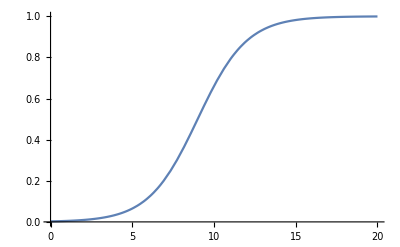

```mathematica
Plot[1/2+Tanh[t/3-3]/2,{t,0,20}]
```